Let’s assume we have two species that share a common ion C:
AC ↔ A + C | K_1 = [A][C]
BC ↔ B + C | K_2= [B][C]

```mathematica
(* define the convex hull of possible solutions *)
```

```mathematica
ch3D=ConvexHullMesh[{{0,0,0},{1,0,0},{0,1,0},{0,0,1}}];
```

```mathematica
k1=0.01;
k2=0.1;
```

```mathematica
acPpt[{a_,b_,c_},acKsp_:k1]:=(c>=acKsp/a)
```

```mathematica
acPpt[{a_,b_,c_},acKsp_:k1]:=If[a==0,False,(c>=acKsp/a)]
```

```mathematica
bcPpt[{a_,b_,c_},bcKsp_:k2]:=If[b==0,False,(c>=bcKsp/b)]
```

```mathematica
ptClfy[{a_,b_,c_}]:=Which[
acPpt[{a,b,c}]&&Not[bcPpt[{a,b,c}]],"ac",
Not[acPpt[{a,b,c}]],"none",
(acPpt[{a,b,c}]&&bcPpt[{a,b,c}]),"either"
]
```

```mathematica
pts=(SeedRandom[1997];
RandomPoint[ch3D,350]);
```

```mathematica
(*{allTrain3D,test3D}=ResourceFunction["TrainTestSplit"][pts,"TestSetSize"->75];
```

```mathematica
(*{startDat3D,pool3D}=ResourceFunction["TrainTestSplit"][allTrain3D,"TestSetSize"->250];
```

```mathematica
allTrain3D=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\allTrainCont3D.csv"];
```

```mathematica
test3D=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\testCont3D.csv"];
```

```mathematica
startDat3D=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\startDatCont3D.csv"];
```

```mathematica
pool3D=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\poolCont3D.csv"];
```

#### Test Plots

```mathematica
test=SemanticImport["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\IBMRxn\\new_organomet_rxns - Sheet1.csv"];
```

```mathematica
test//First//Keys//Normal
```

{reaction number,page number,reaction class,true reaction smiles,notes}

```mathematica
Counts[ptClfy/@pts]
```

<|ac→67,either→7,none→26|>

```mathematica
Show[Plot3D[{k1/a,k2/b}, (*AC and BC equilibrium curves*)
{a,0,1},{b,0,1},
AxesLabel->{"[A]","[B]","[C]"},PlotLegends->{"K_1","K_2"},AspectRatio->1,BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.95],Blue,Opacity[0.95],Yellow}],HighlightMesh[ch3D,Style[2,Opacity[0.5]]],ListPointPlot3D[{Select[pts,acPpt[#]&&Not[bcPpt[#]]&],Select[pts,Not@acPpt[#]&],Select[pts,acPpt[#]&&bcPpt[#]&]},PlotStyle->{Red,Black,Green}]]
```

-Graphics3D-

```mathematica
Show[
With[
{soln1={Sqrt[k1],0,Sqrt[k1]},  (*initial saturated solution of AC*)
soln2={0,Sqrt[k2],Sqrt[k2]}}, (*initial saturated solution of BC*)
Graphics3D[
{Red, Sphere[soln1,0.02], (*initial saturated solution of AC*)
Blue,Sphere[soln2,0.02], (*initial saturated solution of BC*)
Red,Thick,Line[{soln1,soln2}]} (*mixing line*)
]
],
Plot3D[{k1/a,k2/b}, (*AC and BC equilibrium curves*)
{a,0,1},{b,0,1},
AxesLabel->{"[A]","[B]","[C]"},PlotLegends->{"K_1","K_2"},AspectRatio->1,BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.95],Blue,Opacity[0.95],Yellow}]]
```

-Graphics3D-

```mathematica
k1=0.01;
k2=0.15;
```

```mathematica
k1=0.01;
k2=0.15;
Show[
With[
{soln1={Sqrt[k1],0,Sqrt[k1]},  (*initial saturated solution of AC*)
soln2={0,Sqrt[k2],Sqrt[k2]}}, (*initial saturated solution of BC*)
Graphics3D[
{Red, Sphere[soln1,0.02], (*initial saturated solution of AC*)
Blue,Sphere[soln2,0.02], (*initial saturated solution of BC*)
Red,Thick,Line[{soln1,soln2}]} (*mixing line*)
]
],
Plot3D[{k1/a,k2/b}, (*AC and BC equilibrium curves*)
{a,0,1},{b,0,1},
AxesLabel->{"[A]","[B]","[C]"},PlotLegends->{"K_1","K_2"},AspectRatio->1,BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.95],Blue,Opacity[0.95],Yellow}],ListPlot3D[{{0,0,0},{Sqrt[k1],0,Sqrt[k1]},{0,Sqrt[k2],Sqrt[k2]}}]]
```

-Graphics3D-

## Helper Fxns

```mathematica
swapChoice=<|"ac"->{"bc","none","either"},"bc"->{"ac","none","either"},"none"->{"ac","bc","either"},"either"->{"ac","bc","none"}|>;
```

```mathematica
noisyOracle3D[data_,noisePercent_]:=Module[{swap,thread},
swap=Flatten[Table[RandomSample[{noisePercent,1-noisePercent}->{-1,1},1],Length[data]]];(* assign a value {-1,+1} to each example in data given some probability *)
thread=Thread[{(ptClfy/@Normal[data]),swap}];(* thread each ex's class and the random value *)
Which[
#[[2]]==1,(* if the random value is 1 --> *)
#[[1]], (* keep class same *)
#[[2]]==-1,(* if random value is -1 --> *)
First[RandomSample[Table[1/Length[swapChoice[ToString[#[[1]]]]],Length[swapChoice[ToString[#[[1]]]]]]->swapChoice[ToString[#[[1]]]],1]]
]&/@thread
]
```

## Initial Classifier Train

```mathematica
(*clfInit3D=Classify[startDat3D->(ptClfy/@startDat3D),Method->"SupportVectorMachine"]
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D.wmlf",clfInit3D,"WMLF"];
```

```mathematica
clfInit3D=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D.wmlf"];
```

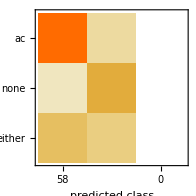
Classifier Measurements
Classifier method | SupportVectorMachine
Number of test examples | 75
Accuracy | (76.5.) %
Accuracy baseline | (71.5.) %
Single evaluation time | 2.96 ms/example
Batch evaluation speed | 9.61 examples/ms
-Graphics- |

```mathematica
clfInit3DMeas=ClassifierMeasurements[clfInit3D,Normal[test3D]->ptClfy/@Normal[test3D]]
```

```mathematica
startDat3D5=Normal[startDat3D[[1;;5]]];
```

```mathematica
(*clfInit3D5=Classify[startDat3D5->ptClfy/@startDat3D5]
```

ClassifierFunction[…]

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D5.wmlf",clfInit3D5,"WMLF"];
```

```mathematica
clfInit3D5=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D5.wmlf"];
```

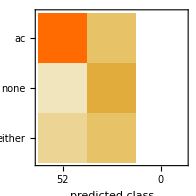
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 75
Accuracy | (73.5.) %
Accuracy baseline | (71.5.) %
Single evaluation time | 2.3 ms/example
Batch evaluation speed | 10.4 examples/ms
-Graphics- |

```mathematica
clfInit3D5Meas=ClassifierMeasurements[clfInit3D5,Normal[test3D]->ptClfy/@Normal[test3D]]
```

### Noise

```mathematica
noisePCs={0.1,0.2,0.3,0.4,0.5};
```

```mathematica
(*{clfInit3D10pc,clfInit3D20pc,clfInit3D30pc,clfInit3D40pc,clfInit3D50pc}=Table[Classify[startDat3D->(noisyOracle3D[startDat3D,noisePCs[[l]]])],{l,1,Length@noisePCs}];
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D50pc.wmlf",clfInit3D50pc,"WMLF"];
```

```mathematica
clfInit3D10pc=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D10pc.wmlf"];
clfInit3D20pc=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D20pc.wmlf"];
clfInit3D30pc=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D30pc.wmlf"];
clfInit3D40pc=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D40pc.wmlf"];
clfInit3D50pc=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D50pc.wmlf"];
```

```mathematica
clfNs={clfInit3D10pc,clfInit3D20pc,clfInit3D30pc,clfInit3D40pc,clfInit3D50pc};
```

```mathematica
(*{clfInit3D10pc5n,clfInit3D20pc5n,clfInit3D30pc5n,clfInit3D40pc5n,clfInit3D50pc5n}=Table[Classify[startDat3D5->(noisyOracle3D[startDat3D5,noisePCs[[l]]])],{l,1,Length@noisePCs}];
```

```mathematica
(*Export["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D50pc5n.wmlf",clfInit3D50pc5n,"WMLF"];
```

```mathematica
clfInit3D10pc5n=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D10pc5n.wmlf"];
clfInit3D20pc5n=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D20pc5n.wmlf"];
clfInit3D30pc5n=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D30pc5n.wmlf"];
clfInit3D40pc5n=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D40pc5n.wmlf"];
clfInit3D50pc5n=Import["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\ternary\\clfInit3D50pc5n.wmlf"];
```

```mathematica
clfNs5={clfInit3D10pc5n,clfInit3D20pc5n,clfInit3D30pc5n,clfInit3D40pc5n,clfInit3D50pc5n};
```

## Grid Search

### Set Up Grid

```mathematica
(* let's try it allowing 120 pts *)
```

```mathematica
grid3D=Table[
If[RegionMember[ch3D,{i,j,k}],{i,j,k},Nothing],{i,0,1,0.14},{j,0,1,0.14},{k,0,1,0.14}
];
```

```mathematica
grid3D=Flatten[grid3D,2];
```

```mathematica
Length@grid3D
```

120

```mathematica
(* more pts *)
```

```mathematica
grid3DMore=Table[
If[RegionMember[ch3D,{i,j,k}],{i,j,k},Nothing],{i,0,1,0.1},{j,0,1,0.1},{k,0,1,0.1}
];
```

```mathematica
grid3DMore=Flatten[grid3DMore,2];
```

```mathematica
Length@grid3DMore
```

286

```mathematica
Show[ListPointPlot3D[grid3D],HighlightMesh[ch3D,Style[2,Opacity[0.5]]]]
```

-Graphics3D-

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsGS3D,tDatGS3D,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[gsSims3D=Table[
Clear[clfsGS3D,tDatGS3D,classif,newDat,tPool,i,newPt];
clfsGS3D={};
tDatGS3D={};
classif=clfInit3D;
newDat=Normal[startDat3D];
tPool=grid3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS3D,classif];
AppendTo[tDatGS3D,newDat];
i++
];
{clfsGS3D,tDatGS3D},
{j,1,numReps}];]
```

{193.566,Null}

```mathematica
gs3DSimTime=193.566;
```

### Simulations - noiseless, starting at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsGS3D5,tDatGS3D5,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[gsSims3D5=Table[
Clear[clfsGS3D5,tDatGS3D5,classif,newDat,tPool,i,newPt];
clfsGS3D5={};
tDatGS3D5={};
classif=clfInit3D5;
newDat=Normal[startDat3D5];
tPool=grid3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS3D5,classif];
AppendTo[tDatGS3D5,newDat];
i++
];
{clfsGS3D5,tDatGS3D5},
{j,1,numReps}];]
```

TakeDrop::iseq: Invalid sequence specification {61} for an expression of length 60.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.,0.14},{0.,0.,0.42},{0.,0.,0.7},{0.,0.,0.98},{0.,0.14,0.14},{0.,0.14,0.42},{0.,0.14,0.7},{0.,0.28,0.},{0.,0.28,0.28},{0.,0.28,0.56},«50»},{61}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {62} for an expression of length 60.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.,0.14},{0.,0.,0.42},{0.,0.,0.7},{0.,0.,0.98},{0.,0.14,0.14},{0.,0.14,0.42},{0.,0.14,0.7},{0.,0.28,0.},{0.,0.28,0.28},{0.,0.28,0.56},«50»},{62}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {63} for an expression of length 60.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.,0.14},{0.,0.,0.42},{0.,0.,0.7},{0.,0.,0.98},{0.,0.14,0.14},{0.,0.14,0.42},{0.,0.14,0.7},{0.,0.28,0.},{0.,0.28,0.28},{0.,0.28,0.56},«50»},{63}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{168.717,Null}

```mathematica
gs3DSimTime=193.566;
```

### Simulations - noiseless - more pts

```mathematica
Length@grid3DMore
```

286

```mathematica
numIts=Length[grid3DMore];(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsGS3D,tDatGS3D,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[gsSims3DMore=Table[
Clear[clfsGS3DMore,tDatGS3DMore,classif,newDat,tPool,i,newPt];
clfsGS3DMore={};
tDatGS3DMore={};
classif=clfInit3D;
newDat=Normal[startDat3D];
tPool=grid3DMore;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS3DMore,classif];
AppendTo[tDatGS3DMore,newDat];
i++
];
{clfsGS3DMore,tDatGS3DMore},
{j,1,numReps}];]
```

TakeDrop::iseq: Invalid sequence specification {144} for an expression of length 143.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.,0.1},{0.,0.,0.3},{0.,0.,0.5},{0.,0.,0.7},{0.,0.,0.9},{0.,0.1,0.},{0.,0.1,0.2},{0.,0.1,0.4},{0.,0.1,0.6},{0.,0.1,0.8},«133»},{144}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {145} for an expression of length 143.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.,0.1},{0.,0.,0.3},{0.,0.,0.5},{0.,0.,0.7},{0.,0.,0.9},{0.,0.1,0.},{0.,0.1,0.2},{0.,0.1,0.4},{0.,0.1,0.6},{0.,0.1,0.8},«133»},{145}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {146} for an expression of length 143.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.,0.1},{0.,0.,0.3},{0.,0.,0.5},{0.,0.,0.7},{0.,0.,0.9},{0.,0.1,0.},{0.,0.1,0.2},{0.,0.1,0.4},{0.,0.1,0.6},{0.,0.1,0.8},«133»},{146}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{778.166,Null}

```mathematica
numIts=100;
```

### Simulations - noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsGS3Dn,tDatGS3Dn,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[{gsSims3D10pc,gsSims3D20pc,gsSims3D30pc,gsSims3D40pc,gsSims3D50pc}=Table[
Table[
Clear[clfsGS3Dn,tDatGS3Dn,classif,newDat,tPool,i,newPt];
clfsGS3Dn={};
tDatGS3Dn={};
classif=clfNs[[l]];
newDat=Normal[startDat3D];
tPool=grid3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS3Dn,classif];
AppendTo[tDatGS3Dn,newDat];
i++
];
{clfsGS3Dn,tDatGS3Dn},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

### Simulations - noise, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsGS3Dn5,tDatGS3Dn5,classif,newDat,tPool]
```

```mathematica
(*AbsoluteTiming[{gsSims3D10pc5,gsSims3D20pc5,gsSims3D30pc5,gsSims3D40pc5,gsSims3D50pc5}=Table[
Table[
Clear[clfsGS3Dn5,tDatGS3Dn5,classif,newDat,tPool,i,newPt];
clfsGS3Dn5={};
tDatGS3Dn5={};
classif=clfNs5[[l]];
newDat=Normal[startDat3D5];
tPool=grid3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsGS3Dn5,classif];
AppendTo[tDatGS3Dn5,newDat];
i++
];
{clfsGS3Dn5,tDatGS3Dn5},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

TakeDrop::iseq: Invalid sequence specification {61} for an expression of length 60.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.,0.14},{0.,0.,0.42},{0.,0.,0.7},{0.,0.,0.98},{0.,0.14,0.14},{0.,0.14,0.42},{0.,0.14,0.7},{0.,0.28,0.},{0.,0.28,0.28},{0.,0.28,0.56},«50»},{61}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {62} for an expression of length 60.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.,0.14},{0.,0.,0.42},{0.,0.,0.7},{0.,0.,0.98},{0.,0.14,0.14},{0.,0.14,0.42},{0.,0.14,0.7},{0.,0.28,0.},{0.,0.28,0.28},{0.,0.28,0.56},«50»},{62}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {63} for an expression of length 60.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.,0.,0.14},{0.,0.,0.42},{0.,0.,0.7},{0.,0.,0.98},{0.,0.14,0.14},{0.,0.14,0.42},{0.,0.14,0.7},{0.,0.28,0.},{0.,0.28,0.28},{0.,0.28,0.56},«50»},{63}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{1182.71,Null}

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3DClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3DClfs=Partition[Map[Import[#]&,gs3DClfPaths],numIts];
```

```mathematica
(*clfGS3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@gSims3D[[All,1]];*)
clfGS3Dmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3DClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3DRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3Dmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$103967080,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$103967080} and TakeDrop[{0.709899,0.290101,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$103967080].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$103967097,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$103967097} and TakeDrop[{0.111842,0.888158,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$103967097].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$103967108,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$103967108} and TakeDrop[{0.786978,0.213022,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$103967108].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.106438,0},{0.109537,0},{0.118298,0},{0.130636,0},{0.131647,0},{0.143162,1},{0.151762,0},{0.157363,0},{0.16499,0},{0.183482,0},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{50,3,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{4,7,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{6,5,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.106438,0},{0.109537,0},{0.118298,0},{0.130636,0},{0.131647,0},{0.143162,1},{0.151762,0},{0.157363,0},{0.16499,0},{0.183482,0},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.106438,0},{0.109537,0},{0.118298,0},{0.130636,0},{0.131647,0},{0.143162,1},{0.151762,0},{0.157363,0},{0.16499,0},{0.183482,0},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

### Analysis - Noiseless, start at 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D5Clfs=Partition[Map[Import[#]&,gs3D5ClfPaths],numIts];
```

```mathematica
(*clfGS3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@gSims3D[[All,1]];*)
clfGS3D5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D5meas]];
```

### Analysis - Noiseless - more pts

```mathematica
numIts=Length[grid3DMore];
```

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3DMoreClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3DMore[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3DMoreClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3DMoreClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3DMoreClfs=Partition[Map[Import[#]&,gs3DMoreClfPaths],numIts];
```

```mathematica
(*clfGS3DMoremeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@gSims3D[[All,1]];*)
clfGS3DMoremeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3DMoreClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3DMoreRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3DMoremeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$185977742,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$185977742} and TakeDrop[{0.709899,0.290101,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$185977742].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$185977763,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$185977763} and TakeDrop[{0.111842,0.888158,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$185977763].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$185977780,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$185977780} and TakeDrop[{0.786978,0.213022,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$185977780].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.106438,0},{0.109537,0},{0.118298,0},{0.130636,0},{0.131647,0},{0.143162,1},{0.151762,0},{0.157363,0},{0.16499,0},{0.183482,0},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{50,3,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{4,7,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{6,5,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.106438,0},{0.109537,0},{0.118298,0},{0.130636,0},{0.131647,0},{0.143162,1},{0.151762,0},{0.157363,0},{0.16499,0},{0.183482,0},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.106438,0},{0.109537,0},{0.118298,0},{0.130636,0},{0.131647,0},{0.143162,1},{0.151762,0},{0.157363,0},{0.16499,0},{0.183482,0},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
numIts=100;
```

### Analysis - noise

#### 10%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D10pcClfs=Partition[Map[Import[#]&,gs3D10pcClfPaths],numIts];
```

```mathematica
clfGS3D10pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D10pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D10pcmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$104676437,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$104676437} and TakeDrop[{0.885469,0.00954835,0.104983,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$104676437].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$104676456,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$104676456} and TakeDrop[{0.848299,0.00985812,0.141843,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$104676456].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$104676473,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$104676473} and TakeDrop[{0.888,0.0092392,0.102761,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$104676473].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0992755,0},{0.0992939,1},{0.0992985,0},{0.0993776,0},{0.100044,1},{0.100354,0},{0.100401,0},{0.100604,0},{0.101433,0},{0.101749,0},«80»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{53,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{11,0,0,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0656978,0},{0.0668624,0},{0.0678119,0},{0.0678944,0},{0.0683369,0},{0.0698707,0},{0.0699635,0},{0.0701158,0},{0.070464,1},{0.0731178,0},«88»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0656978,0},{0.0668624,0},{0.0678119,0},{0.0678944,0},{0.0683369,0},{0.0698707,0},{0.0699635,0},{0.0701158,0},{0.070464,1},{0.0731178,0},«88»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

#### 20%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D20pcClfs=Partition[Map[Import[#]&,gs3D20pcClfPaths],numIts];
```

```mathematica
clfGS3D20pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D20pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D20pcmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$105417672,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$105417672} and TakeDrop[{0.589758,0.00984175,0.4004,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$105417672].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$105417691,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$105417691} and TakeDrop[{0.00461095,0.00923698,0.986152,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$105417691].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$105417708,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$105417708} and TakeDrop[{0.776233,0.00900864,0.214759,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$105417708].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0499917,0},{0.0505644,1},{0.0590041,0},{0.060596,0},{0.0611893,0},{0.0627896,0},{0.072345,0},{0.074761,0},{0.0766021,0},{0.0965508,0},«93»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{48,0,5,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{5,0,6,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0631683,0},{0.0662159,0},{0.0679246,0},{0.0681796,0},{0.0682284,0},{0.068249,0},{0.068522,0},{0.0687209,0},{0.0692533,0},{0.0717938,0},«107»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.195488,0},{0.196017,0},{0.197409,1},{0.198241,0},{0.198436,0},{0.202121,0},{0.203299,0},{0.204891,0},{0.205553,0},{0.2082,0},«151»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

#### 30%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D30pcClfs=Partition[Map[Import[#]&,gs3D30pcClfPaths],numIts];
```

```mathematica
clfGS3D30pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D30pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D30pcmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106156102,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$106156102} and TakeDrop[{0.649545,0.0546017,0.295853,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106156102].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106156121,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$106156121} and TakeDrop[{0.463757,0.0546012,0.481642,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106156121].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106156138,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$106156138} and TakeDrop[{0.758714,0.0556306,0.185656,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106156138].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.124712,0},{0.130219,0},{0.133358,0},{0.135456,0},{0.139011,0},{0.139636,0},{0.142245,0},{0.142794,0},{0.143573,0},{0.145961,0},«99»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{53,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{10,0,1,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

#### 40%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D40pcClfs=Partition[Map[Import[#]&,gs3D40pcClfPaths],numIts];
```

```mathematica
clfGS3D40pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D40pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D40pcmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106887634,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$106887634} and TakeDrop[{0.403109,0.182219,0.414673,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106887634].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106887651,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$106887651} and TakeDrop[{0.400664,0.183727,0.415609,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106887651].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106887670,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$106887670} and TakeDrop[{0.403777,0.188998,0.407225,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$106887670].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.384835,0},{0.384992,0},{0.385426,0},{0.387299,0},{0.387348,0},{0.387554,0},{0.38778,1},{0.387816,0},{0.387926,0},{0.389075,0},«113»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{43,0,10,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{3,0,8,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.255672,1},{0.256097,1},{0.256099,1},{0.256137,1},{0.256163,1},{0.256208,1},{0.256347,1},{0.256405,1},{0.25655,1},{0.256578,1},«179»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

#### 50%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D50pcClfs=Partition[Map[Import[#]&,gs3D50pcClfPaths],numIts];
```

```mathematica
clfGS3D50pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D50pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D50pcmeas];
```

### Analysis - noise, start at 5 - comment table

#### 10%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D10pc5Clfs=Partition[Map[Import[#]&,gs3D10pc5ClfPaths],numIts];
```

```mathematica
clfGS3D10pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D10pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D10pc5meas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$253074024,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$253074024} and TakeDrop[{0.817465,0.089463,0.0930721,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$253074024].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$253074043,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$253074043} and TakeDrop[{0.82454,0.0858722,0.0895874,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$253074043].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$253074060,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$253074060} and TakeDrop[{0.818016,0.0877446,0.0942392,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$253074060].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0889176,0},{0.0890667,0},{0.0891416,0},{0.0891439,0},{0.0892974,0},{0.0893093,0},{0.0893134,0},{0.0893602,0},{0.0893657,0},{0.0893977,0},«142»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{53,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{11,0,0,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0284485,0},{0.0314179,0},{0.0318462,0},{0.0412194,0},{0.0477433,0},{0.0480103,0},{0.0512441,0},{0.0515185,0},{0.0553542,1},{0.0576123,0},«104»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0284485,0},{0.0314179,0},{0.0318462,0},{0.0412194,0},{0.0477433,0},{0.0480103,0},{0.0512441,0},{0.0515185,0},{0.0553542,1},{0.0576123,0},«104»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

#### 20%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D20pc5Clfs=Partition[Map[Import[#]&,gs3D20pc5ClfPaths],numIts];
```

```mathematica
clfGS3D20pcn5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D20pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D20pc5meas];
```

#### 30%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D30pc5Clfs=Partition[Map[Import[#]&,gs3D30pc5ClfPaths],numIts];
```

```mathematica
clfGS3D30pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D30pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D30pc5meas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$254422811,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$254422811} and TakeDrop[{0.499889,0.500111,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$254422811].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$254422830,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$254422830} and TakeDrop[{0.500013,0.499987,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$254422830].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$254422847,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$254422847} and TakeDrop[{0.499992,0.500008,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$254422847].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.499728,0},{0.499746,0},{0.499749,0},{0.499776,0},{0.499777,1},{0.499781,0},{0.499784,0},{0.499799,0},{0.4998,0},{0.499807,1},«114»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{34,19,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{4,7,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{2,9,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.021167,0},{0.0215627,0},{0.0248046,0},{0.0278471,0},{0.0299246,0},{0.0299527,0},{0.0303799,0},{0.0303907,0},{0.0305895,0},{0.0328392,0},«107»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.281131,0},{0.281323,1},{0.281796,1},{0.281922,0},{0.282205,1},{0.282253,1},{0.282951,1},{0.283307,1},{0.283388,0},{0.283754,1},«115»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

#### 40%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D40pc5Clfs=Partition[Map[Import[#]&,gs3D40pc5ClfPaths],numIts];
```

```mathematica
clfGS3D40pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D40pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D40pc5meas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255189619,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$255189619} and TakeDrop[{0.333281,0.333465,0.333254,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255189619].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255189638,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$255189638} and TakeDrop[{0.333205,0.333334,0.333461,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255189638].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255189655,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$255189655} and TakeDrop[{0.333347,0.333388,0.333265,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255189655].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.333183,0},{0.333184,0},{0.333186,0},{0.333189,0},{0.333191,0},{0.333198,0},{0.3332,0},{0.333205,0},{0.333206,0},{0.333209,0},«166»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{33,14,6,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{2,0,9,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.00419061,1},{0.0041915,1},{0.00532017,1},{0.00556348,1},{0.00560262,0},{0.00578175,1},{0.0059613,1},{0.0062073,1},{0.00648859,1},{0.00665433,1},«111»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0649386,0},{0.0649678,1},{0.0649726,0},{0.0650309,1},{0.0651627,1},{0.0651828,1},{0.0651846,1},{0.0652145,1},{0.0653513,1},{0.0653847,1},«180»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

#### 50%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],gsSims3D50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
gs3D50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\gs3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
gs3D50pc5Clfs=Partition[Map[Import[#]&,gs3D50pc5ClfPaths],numIts];
```

```mathematica
clfGS3D50pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@gs3D50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
gs3D50pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfGS3D50pc5meas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255987404,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$255987404} and TakeDrop[{0.333359,0.333398,0.333243,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255987404].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255987421,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$255987421} and TakeDrop[{0.333351,0.333177,0.333472,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255987421].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255987440,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$255987440} and TakeDrop[{0.333354,0.333386,0.333261,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$255987440].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.333185,0},{0.333185,0},{0.333185,0},{0.333185,0},{0.333187,0},{0.333188,0},{0.333192,0},{0.333193,0},{0.333194,0},{0.333195,0},«151»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{7,39,7,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,2,9,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0112126,0},{0.0139296,1},{0.0140452,0},{0.015898,1},{0.0196534,0},{0.0228911,0},{0.0253757,1},{0.0295948,0},{0.0308581,0},{0.0341802,0},«52»},Min[71,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.167326,1},{0.167431,0},{0.167671,1},{0.16774,1},{0.168057,1},{0.168128,1},{0.168185,1},{0.168373,1},{0.168566,1},{0.16881,0},«110»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

## Serial Dilution Rays

### Code up the ray points

```mathematica
(* defines the line given two points and outputs the y given an x *)
```

```mathematica
getLine[{x1:0,y1:0},{x2_,y2_},x_]:=Module[{m,b=0},
m=((y2-y1)/(x2-x1));
m*x+b
]
```

```mathematica
upBounds3D=Table[First[ReverseSortBy[Select[grid3D,#[[1;;2]]==DeleteDuplicates[grid3D[[All,1;;2]]][[i]]&],#[[3]]&]],{i,1,Length[DeleteDuplicates[grid3D[[All,1;;2]]]]}];
```

```mathematica
upBounds3D=Select[upBounds3D,Not[MemberQ[#,0.0]]&];
```

```mathematica
ListPointPlot3D@upBounds3D
```

-Graphics3D-

```mathematica
getSpherical[{x_,y_,z_}]:=Module[{r,θ,ϕ},
r=Sqrt[x^2+y^2+z^2];
θ=ArcTan[y/x];
ϕ=ArcTan[Sqrt[x^2+y^2]/z];
{r,θ,ϕ}
]
```

```mathematica
getCart[{r_,θ_,ϕ_}]:=Module[{x,y,z},
x=r*Sin[ϕ]*Cos[θ];
y=r*Sin[ϕ]*Sin[θ];
z=r*Cos[ϕ];
{x,y,z}
]
```

```mathematica
SetPrecision[getSpherical[upBounds3D[[1]]][[1]],4]/10
```

0.07275

```mathematica
getDilutePts[{x_,y_,z_},n_]:=Module[{spher,r0,incs,rs,sphers},
spher=getSpherical[{x,y,z}];
r0=spher[[1]];
incs=SetPrecision[r0,4]/n;
rs=Range[0,r0,incs];
sphers=Table[{i,spher[[2]],spher[[3]]},{i,rs}];
Map[getCart[#]&,sphers]
]
```

```mathematica
Length@DeleteDuplicates[Flatten[(getDilutePts[#,7]&/@upBounds3D),1]]
```

106

```mathematica
rayPts3D=Rest[DeleteDuplicates[Flatten[(getDilutePts[#,7]&/@upBounds3D),1]]];
```

```mathematica
ListPointPlot3D@rayPts3D
```

-Graphics3D-

### Simulations - Noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[rdSims3D=Table[
Clear[clfsRD3D,tDatRD3D,classif,newDat,tPool,i,newPt];
clfsRD3D={};
tDatRD3D={};
classif=clfInit3D;
newDat=startDat3D;
tPool=rayPts3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRD3D,classif];
AppendTo[tDatRD3D,newDat];
i++
];
{clfsRD3D,tDatRD3D},
{j,1,numReps}];]
```

{184.331,Null}

```mathematica
rd3DSimTime=184.331;
```

### Simulations - Noiseless, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[rdSims3D5=Table[
Clear[clfsRD3D5,tDatRD3D5,classif,newDat,tPool,i,newPt];
clfsRD3D5={};
tDatRD3D5={};
classif=clfInit3D5;
newDat=startDat3D5;
tPool=rayPts3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRD3D5,classif];
AppendTo[tDatRD3D5,newDat];
i++
];
{clfsRD3D5,tDatRD3D5},
{j,1,numReps}];]
```

TakeDrop::iseq: Invalid sequence specification {54} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.04,0.04,0.2},{0.08,0.08,0.4},{0.12,0.12,0.6},{0.02,0.04,0.08},{0.06,0.12,0.24},{«1»},{«20»,0.28,«19»},{0.04,0.12,0.12},{0.08,0.24,0.24},{0.12,0.36,0.36},«42»},«1»] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {55} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.04,0.04,0.2},{0.08,0.08,0.4},{0.12,0.12,0.6},{0.02,0.04,0.08},{0.06,0.12,0.24},{«1»},{«20»,0.28,«19»},{0.04,0.12,0.12},{0.08,0.24,0.24},{0.12,0.36,0.36},«42»},«1»] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {56} for an expression of length 52.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.04,0.04,0.2},{0.08,0.08,0.4},{0.12,0.12,0.6},{0.02,0.04,0.08},{0.06,0.12,0.24},{«1»},{«20»,0.28,«19»},{0.04,0.12,0.12},{0.08,0.24,0.24},{0.12,0.36,0.36},«42»},«1»] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{178.968,Null}

```mathematica
rd3DSimTime=184.331;
```

### Simulations - noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[{rdSims3D10pc,rdSims3D20pc,rdSims3D30pc,rdSims3D40pc,rdSims3D50pc}=Table[
Table[
Clear[clfsRD3Dn,tDatRD3Dn,classif,newDat,tPool,i,newPt];
clfsRD3Dn={};
tDatRD3Dn={};
classif=clfNs[[l]];
newDat=Normal[startDat3D];
tPool=rayPts3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRD3Dn,classif];
AppendTo[tDatRD3Dn,newDat];
i++
];
{clfsRD3Dn,tDatRD3Dn},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

TakeDrop::iseq: Invalid sequence specification {54} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[«1»,{54}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {55} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[«1»,{55}] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {56} for an expression of length 52.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[«1»,{56}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

{1300.71,Null}

### Simulations - noise, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
AbsoluteTiming[{rdSims3D10pc5,rdSims3D20pc5,rdSims3D30pc5,rdSims3D40pc5,rdSims3D50pc5}=Table[
Table[
Clear[clfsRD3Dn5,tDatRD3Dn5,classif,newDat,tPool,i,newPt];
clfsRD3Dn5={};
tDatRD3Dn5={};
classif=clfNs5[[l]];
newDat=Normal[startDat3D5];
tPool=rayPts3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{i}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRD3Dn5,classif];
AppendTo[tDatRD3Dn5,newDat];
i++
];
{clfsRD3Dn5,tDatRD3Dn5},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

TakeDrop::iseq: Invalid sequence specification {54} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.04,0.04,0.2},{0.08,0.08,0.4},{0.12,0.12,0.6},{0.02,0.04,0.08},{0.06,0.12,0.24},{«1»},{«20»,0.28,«19»},{0.04,0.12,0.12},{0.08,0.24,0.24},{0.12,0.36,0.36},«42»},«1»] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {55} for an expression of length 52.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.04,0.04,0.2},{0.08,0.08,0.4},{0.12,0.12,0.6},{0.02,0.04,0.08},{0.06,0.12,0.24},{«1»},{«20»,0.28,«19»},{0.04,0.12,0.12},{0.08,0.24,0.24},{0.12,0.36,0.36},«42»},«1»] are not the same shape.

TakeDrop::iseq: Invalid sequence specification {56} for an expression of length 52.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {newPt,tPool} and TakeDrop[{{0.04,0.04,0.2},{0.08,0.08,0.4},{0.12,0.12,0.6},{0.02,0.04,0.08},{0.06,0.12,0.24},{«1»},{«20»,0.28,«19»},{0.04,0.12,0.12},{0.08,0.24,0.24},{0.12,0.36,0.36},«42»},«1»] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

$Aborted

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3DClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3DClfs=Partition[Map[Import[#]&,rd3DClfPaths],numIts];
```

```mathematica
(*clfRD3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@rdSims3D[[All,1]];*)
clfRD3Dmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3DClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3DRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3Dmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$108303762,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$108303762} and TakeDrop[{0.725845,0.274155,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$108303762].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$108303781,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$108303781} and TakeDrop[{0.130768,0.869232,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$108303781].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$108303798,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$108303798} and TakeDrop[{0.79028,0.20972,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$108303798].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.1195,0},{0.119953,0},{0.12283,0},{0.135947,0},{0.151604,0},{0.157854,1},{0.163366,0},{0.164205,0},{0.183377,0},{0.207913,0},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{47,6,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{4,7,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{6,5,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.1195,0},{0.119953,0},{0.12283,0},{0.135947,0},{0.151604,0},{0.157854,1},{0.163366,0},{0.164205,0},{0.183377,0},{0.207913,0},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.1195,0},{0.119953,0},{0.12283,0},{0.135947,0},{0.151604,0},{0.157854,1},{0.163366,0},{0.164205,0},{0.183377,0},{0.207913,0},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

### Analysis - Noiseless, start at 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D5Clfs=Partition[Map[Import[#]&,rd3D5ClfPaths],numIts];
```

```mathematica
(*clfRD3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@rdSims3D[[All,1]];*)
clfRD3D5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D5meas]];
```

### Analysis - noise

#### 10%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D10pcClfs=Partition[Map[Import[#]&,rd3D10pcClfPaths],numIts];
```

```mathematica
clfRD3D10pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D10pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D10pcmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011431,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109011431} and TakeDrop[{0.599905,0.400095,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011431].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011450,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109011450} and TakeDrop[{0.00903342,0.990967,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011450].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011467,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109011467} and TakeDrop[{0.953846,0.0461536,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011467].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.034201,0},{0.0371189,1},{0.0409284,0},{0.0424234,0},{0.05012,0},{0.0523372,0},{0.056465,0},{0.0572828,0},{0.0654429,0},{0.0673671,1},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{47,6,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{3,8,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{6,5,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.084109,0},{0.0842272,1},{0.0842327,0},{0.0842808,0},{0.0845965,0},{0.0850619,0},{0.0852205,0},{0.0852463,0},{0.085248,0},{0.0852531,1},«89»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.104921,0},{0.118864,0},{0.120187,0},{0.121595,0},{0.124146,0},{0.1266,0},{0.128549,0},{0.133174,0},{0.133965,0},{0.135493,0},«111»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

#### 20%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D20pcClfs=Partition[Map[Import[#]&,rd3D20pcClfPaths],numIts];
```

```mathematica
clfRD3D20pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D20pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D20pcmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738299,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109738299} and TakeDrop[{0.850693,0.0126323,0.136674,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738299].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738318,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109738318} and TakeDrop[{0.117676,0.0078334,0.87449,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738318].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738335,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109738335} and TakeDrop[{0.896823,0.011913,0.0912643,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738335].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.095633,0},{0.102942,0},{0.106889,0},{0.11985,0},{0.12715,0},{0.132185,0},{0.136457,0},{0.143388,1},{0.155421,0},{0.155447,0},«84»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{49,0,4,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{2,0,9,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0453538,0},{0.0481037,0},{0.0491777,0},{0.0497392,0},{0.0531424,0},{0.0563875,0},{0.0570554,0},{0.0572762,0},{0.0585384,0},{0.0623451,0},«99»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0347974,0},{0.0349565,0},{0.0373308,0},{0.0389288,0},{0.0397365,0},{0.0441677,0},{0.0486309,0},{0.0486986,0},{0.051434,0},{0.056097,0},«91»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

#### 30%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D30pcClfs=Partition[Map[Import[#]&,rd3D30pcClfPaths],numIts];
```

```mathematica
clfRD3D30pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D30pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D30pcmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475460,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$110475460} and TakeDrop[{0.88045,0.0484814,0.0710689,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475460].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475479,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$110475479} and TakeDrop[{0.875551,0.0416252,0.0828243,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475479].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475496,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$110475496} and TakeDrop[{0.876369,0.0459299,0.0777008,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475496].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0879297,0},{0.08794,0},{0.0882705,0},{0.0885106,0},{0.0889043,0},{0.0890196,0},{0.0892239,0},{0.0893007,0},{0.0896627,0},{0.0901396,0},«95»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{53,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{11,0,0,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

#### 40%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D40pcClfs=Partition[Map[Import[#]&,rd3D40pcClfPaths],numIts];
```

```mathematica
clfRD3D40pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D40pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D40pcmeas];
```

#### 50%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D50pcClfs=Partition[Map[Import[#]&,rd3D50pcClfPaths],numIts];
```

```mathematica
clfRD3D50pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D50pcRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D50pcmeas];
```

### Analysis - noise, start at 5

#### 10%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D10pc5Clfs=Partition[Map[Import[#]&,rd3D10pc5ClfPaths],numIts];
```

```mathematica
clfRD3D10pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D10pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D10pc5meas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011431,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109011431} and TakeDrop[{0.599905,0.400095,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011431].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011450,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109011450} and TakeDrop[{0.00903342,0.990967,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011450].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011467,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109011467} and TakeDrop[{0.953846,0.0461536,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109011467].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.034201,0},{0.0371189,1},{0.0409284,0},{0.0424234,0},{0.05012,0},{0.0523372,0},{0.056465,0},{0.0572828,0},{0.0654429,0},{0.0673671,1},«82»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{47,6,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{3,8,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{6,5,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.084109,0},{0.0842272,1},{0.0842327,0},{0.0842808,0},{0.0845965,0},{0.0850619,0},{0.0852205,0},{0.0852463,0},{0.085248,0},{0.0852531,1},«89»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.104921,0},{0.118864,0},{0.120187,0},{0.121595,0},{0.124146,0},{0.1266,0},{0.128549,0},{0.133174,0},{0.133965,0},{0.135493,0},«111»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

#### 20%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D20pc5Clfs=Partition[Map[Import[#]&,rd3D20pc5ClfPaths],numIts];
```

```mathematica
clfRD3D20pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D20pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D20pc5meas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738299,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109738299} and TakeDrop[{0.850693,0.0126323,0.136674,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738299].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738318,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109738318} and TakeDrop[{0.117676,0.0078334,0.87449,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738318].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738335,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$109738335} and TakeDrop[{0.896823,0.011913,0.0912643,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$109738335].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.095633,0},{0.102942,0},{0.106889,0},{0.11985,0},{0.12715,0},{0.132185,0},{0.136457,0},{0.143388,1},{0.155421,0},{0.155447,0},«84»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{49,0,4,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{2,0,9,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0453538,0},{0.0481037,0},{0.0491777,0},{0.0497392,0},{0.0531424,0},{0.0563875,0},{0.0570554,0},{0.0572762,0},{0.0585384,0},{0.0623451,0},«99»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0347974,0},{0.0349565,0},{0.0373308,0},{0.0389288,0},{0.0397365,0},{0.0441677,0},{0.0486309,0},{0.0486986,0},{0.051434,0},{0.056097,0},«91»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

#### 30%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D30pc5Clfs=Partition[Map[Import[#]&,rd3D30pc5ClfPaths],numIts];
```

```mathematica
clfRD3D30pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D30pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D30pc5meas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475460,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$110475460} and TakeDrop[{0.88045,0.0484814,0.0710689,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475460].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475479,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$110475479} and TakeDrop[{0.875551,0.0416252,0.0828243,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475479].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 4.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475496,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$110475496} and TakeDrop[{0.876369,0.0459299,0.0777008,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$110475496].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0879297,0},{0.08794,0},{0.0882705,0},{0.0885106,0},{0.0889043,0},{0.0890196,0},{0.0892239,0},{0.0893007,0},{0.0896627,0},{0.0901396,0},«95»},Min[134,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{53,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{0,0,0,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,bc,none,Indeterminate}→{11,0,0,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

#### 40%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D40pc5Clfs=Partition[Map[Import[#]&,rd3D40pc5ClfPaths],numIts];
```

```mathematica
clfRD3D40pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D40pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D40pc5meas];
```

#### 50%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],rdSims3D50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
rd3D50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\rd3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
rd3D50pc5Clfs=Partition[Map[Import[#]&,rd3D50pc5ClfPaths],numIts];
```

```mathematica
clfRD3D50pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@rd3D50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
rd3D50pc5Res=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRD3D50pc5meas];
```

## Random Add

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[raSims3D=Table[
Clear[clfsRA3D,tDatRA3D,classif,newDat,tPool,i,newPt];
clfsRA3D={};
tDatRA3D={};
classif=clfInit3D;
newDat=startDat3D;
tPool=pool3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{RandomInteger[{1,Length@tPool}]}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRA3D,classif];
AppendTo[tDatRA3D,newDat];
i++
];
{clfsRA3D,tDatRA3D},
{j,1,numReps}];]
```

{194.671,Null}

```mathematica
ra3DSimTime=194.671;
```

### Simulations - noiseless, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[raSims3D5=Table[
Clear[clfsRA3D5,tDatRA3D5,classif,newDat,tPool,i,newPt];
clfsRA3D5={};
tDatRA3D5={};
classif=clfInit3D5;
newDat=startDat3D5;
tPool=pool3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{RandomInteger[{1,Length@tPool}]}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRA3D5,classif];
AppendTo[tDatRA3D5,newDat];
i++
];
{clfsRA3D5,tDatRA3D5},
{j,1,numReps}];]
```

{194.909,Null}

```mathematica
ra3DSimTime=194.671;
```

### Simulations - noiseless - more

```mathematica
numIts=Length[pool3D];(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
AbsoluteTiming[raSims3DMore=Table[
Clear[clfsRA3DMore,tDatRA3DMore,classif,newDat,tPool,i,newPt];
clfsRA3DMore={};
tDatRA3DMore={};
classif=clfInit3D;
newDat=startDat3D;
tPool=pool3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{RandomInteger[{1,Length@tPool}]}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRA3DMore,classif];
AppendTo[tDatRA3DMore,newDat];
i++
];
{clfsRA3DMore,tDatRA3DMore},
{j,1,numReps}];]
```

{730.782,Null}

### Simulations - noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[{raSims3D10pc,raSims3D20pc,raSims3D30pc,raSims3D40pc,raSims3D50pc}=Table[Table[
Clear[clfsRA3Dn,tDatRA3Dn,classif,newDat,tPool,i,newPt];
clfsRA3Dn={};
tDatRA3Dn={};
classif=clfNs[[l]];
newDat=startDat3D;
tPool=pool3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{RandomInteger[{1,Length@tPool}]}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRA3Dn,classif];
AppendTo[tDatRA3Dn,newDat];
i++
];
{clfsRA3Dn,tDatRA3Dn},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

### Simulations - noise, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
AbsoluteTiming[{raSims3D10pc5,raSims3D20pc5,raSims3D30pc5,raSims3D40pc5,raSims3D50pc5}=Table[Table[
Clear[clfsRA3Dn5,tDatRA3Dn5,classif,newDat,tPool,i,newPt];
clfsRA3Dn5={};
tDatRA3Dn5={};
classif=clfNs5[[l]];
newDat=startDat3D5;
tPool=pool3D;
i=1;
While[i<=numIts,
{newPt,tPool}=TakeDrop[tPool,{RandomInteger[{1,Length@tPool}]}];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsRA3Dn5,classif];
AppendTo[tDatRA3Dn5,newDat];
i++
];
{clfsRA3Dn5,tDatRA3Dn5},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3DClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3DClfs=Partition[Map[Import[#]&,ra3DClfPaths],numIts];
```

```mathematica
(*clfRA3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test3D)]&/@#&/@raSims3D[[All,1]];*)
clfRA3Dmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3DClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3DRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3Dmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$112598467,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$112598467} and TakeDrop[{0.747171,0.252829,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$112598467].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$112598486,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$112598486} and TakeDrop[{0.324815,0.675185,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$112598486].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$112598503,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$112598503} and TakeDrop[{0.865897,0.134103,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$112598503].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.158614,0},{0.164131,0},{0.164922,0},{0.166345,1},{0.175876,0},{0.218127,0},{0.229119,0},{0.23146,0},{0.249931,0},{0.26844,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{51,2,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{6,5,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{9,2,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.102844,0},{0.120493,1},{0.129893,0},{0.13326,0},{0.137924,0},{0.146567,0},{0.158649,0},{0.161452,0},{0.161593,0},{0.162755,1},«79»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.158665,0},{0.164104,0},{0.164682,0},{0.166383,1},{0.175828,0},{0.218378,0},{0.229112,0},{0.231454,0},{0.249731,0},{0.268727,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

### Analysis - Noiseless, start at 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D5Clfs=Partition[Map[Import[#]&,ra3D5ClfPaths],numIts];
```

```mathematica
(*clfRA3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test3D)]&/@#&/@raSims3D[[All,1]];*)
clfRA3D5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D5meas]];
```

### Analysis - Noiseless - more

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3DMoreClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3DMore[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3DMoreClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3DMoreClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3DMoreClfs=Partition[Map[Import[#]&,ra3DMoreClfPaths],numIts];
```

```mathematica
(*clfRA3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test3D)]&/@#&/@raSims3D[[All,1]];*)
clfRA3DMoremeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3DMoreClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3DMoreRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3DMoremeas];
```

### Analysis - noise

#### 10%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D10pcClfs=Partition[Map[Import[#]&,ra3D10pcClfPaths],numIts];
```

```mathematica
clfRA3D10pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D10pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D10pcmeas]];
```

#### 20%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D20pcClfs=Partition[Map[Import[#]&,ra3D20pcClfPaths],numIts];
```

```mathematica
clfRA3D20pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D20pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D20pcmeas]];
```

#### 30%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D30pcClfs=Partition[Map[Import[#]&,ra3D30pcClfPaths],numIts];
```

```mathematica
clfRA3D30pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D30pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D30pcmeas]];
```

#### 40%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D40pcClfs=Partition[Map[Import[#]&,ra3D40pcClfPaths],numIts];
```

```mathematica
clfRA3D40pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D40pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D40pcmeas]];
```

#### 50%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D50pcClfs=Partition[Map[Import[#]&,ra3D50pcClfPaths],numIts];
```

```mathematica
clfRA3D50pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D50pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D50pcmeas]];
```

### Analysis - noise, start at 5

#### 10%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D10pc5Clfs=Partition[Map[Import[#]&,ra3D10pc5ClfPaths],numIts];
```

```mathematica
clfRA3D10pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D10pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D10pc5meas]];
```

#### 20%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D20pc5Clfs=Partition[Map[Import[#]&,ra3D20pc5ClfPaths],numIts];
```

```mathematica
clfRA3D20pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D20pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D20pc5meas]];
```

#### 30%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D30pc5Clfs=Partition[Map[Import[#]&,ra3D30pc5ClfPaths],numIts];
```

```mathematica
clfRA3D30pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D30pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D30pc5meas]];
```

#### 40%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D40pc5Clfs=Partition[Map[Import[#]&,ra3D40pc5ClfPaths],numIts];
```

```mathematica
clfRA3D40pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D40pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D40pc5meas]];
```

#### 50%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],raSims3D50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ra3D50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ra3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ra3D50pc5Clfs=Partition[Map[Import[#]&,ra3D50pc5ClfPaths],numIts];
```

```mathematica
clfRA3D50pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ra3D50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ra3D50pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfRA3D50pc5meas]];
```

## Uncertainty

```mathematica
getWeights[clf_ClassifierFunction,data_,form_:"flat"]:=Module[{tfProbs,entropy,numClusts},
(* Inputs a classifier and test/state set data, finds entropy and puts it through a LogisticSigmoid *)
Which[form=="flat",
tfProbs=Values[clf[data,"Probabilities"]];
entropy=Map[((-#[[1]]*Log[#[[1]]])-(#[[2]]*Log[#[[2]]]))&,tfProbs];
SoftmaxLayer[][entropy],

form=="cluster",(* probably should just flatten, compute, reshape, but idk *)
numClusts=Length[data];
Table[getWeights[clf,data[[i]],"flat"]
,{i,1,numClusts}]
]]
```

```mathematica
getWeights[clf_ClassifierFunction,data_,form_:"flat",out_:"softmax"]:=Module[{tfProbs,entropy,numClusts},
(* Inputs a classifier and test/state set data, finds entropy and puts it through a LogisticSigmoid *)
Which[form=="flat",
tfProbs=Values[clf[data,"Probabilities"]];
entropy=Map[((-#[[1]]*Log[#[[1]],2])-(#[[2]]*Log[#[[2]],2]))&,tfProbs];
Which[out=="softmax",
SoftmaxLayer[][entropy],
out=="entropy",
entropy],

form=="cluster",(* probably should just flatten, compute, reshape, but idk *)
numClusts=Length[data];
Table[getWeights[clf,data[[i]],"flat"]
,{i,1,numClusts}]
]]
```

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsU3D,tDatU3D]
```

```mathematica
(*AbsoluteTiming[uSims3D=Table[
Clear[clfsU3D,tDatU3D,classif,newDat,tPool,i,newPt];
clfsU3D={};
tDatU3D={};
classif=clfInit3D;
newDat=Normal[startDat3D];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
weights=getWeights[classif,tPool];
{newPt,tPool}=TakeDrop[tPool,RandomSample[getWeights[classif,tPool]->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsU3D,classif];
AppendTo[tDatU3D,newDat];
i++
];
{clfsU3D,tDatU3D},
{j,1,numReps}];]
```

{205.303,Null}

```mathematica
u3DSimTime=205.303;
```

### Simulations - noiseless, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsU3D,tDatU3D]
```

```mathematica
(*AbsoluteTiming[uSims3D5=Table[
Clear[clfsU3D5,tDatU3D5,classif,newDat,tPool,i,newPt];
clfsU3D5={};
tDatU3D5={};
classif=clfInit3D5;
newDat=Normal[startDat3D5];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
weights=getWeights[classif,tPool];
{newPt,tPool}=TakeDrop[tPool,RandomSample[getWeights[classif,tPool]->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsU3D5,classif];
AppendTo[tDatU3D5,newDat];
i++
];
{clfsU3D5,tDatU3D5},
{j,1,numReps}];]
```

{208.217,Null}

```mathematica
u3DSimTime=205.303;
```

### Simulations - noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsU3D,tDatU3D]
```

```mathematica
(*AbsoluteTiming[{uSims3D10pc,uSims3D20pc,uSims3D30pc,uSims3D40pc,uSims3D50pc}=Table[Table[
Clear[clfsU3Dn,tDatU3Dn,classif,newDat,tPool,i,newPt];
clfsU3Dn={};
tDatU3Dn={};
classif=clfNs[[l]];
newDat=Normal[startDat3D];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
weights=getWeights[classif,tPool];
{newPt,tPool}=TakeDrop[tPool,RandomSample[getWeights[classif,tPool]->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsU3Dn,classif];
AppendTo[tDatU3Dn,newDat];
i++
];
{clfsU3Dn,tDatU3Dn},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

### Simulations - noise, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
Clear[clfsU3D,tDatU3D]
```

```mathematica
AbsoluteTiming[{uSims3D10pc5,uSims3D20pc5,uSims3D30pc5,uSims3D40pc5,uSims3D50pc5}=Table[Table[
Clear[clfsU3Dn5,tDatU3Dn5,classif,newDat,tPool,i,newPt];
clfsU3Dn5={};
tDatU3Dn5={};
classif=clfNs5[[l]];
newDat=Normal[startDat3D5];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
weights=getWeights[classif,tPool];
{newPt,tPool}=TakeDrop[tPool,RandomSample[getWeights[classif,tPool]->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsU3Dn5,classif];
AppendTo[tDatU3Dn5,newDat];
i++
];
{clfsU3Dn5,tDatU3Dn5},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3DClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3DClfs=Partition[Map[Import[#]&,u3DClfPaths],numIts];
```

```mathematica
(*clfU3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test3D)]&/@#&/@uSims3D[[All,1]];*)
clfU3Dmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3DClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3DRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3Dmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$116757337,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$116757337} and TakeDrop[{0.777349,0.222651,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$116757337].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$116757356,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$116757356} and TakeDrop[{0.0778251,0.922175,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$116757356].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$116757373,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$116757373} and TakeDrop[{0.795385,0.204615,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$116757373].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.100072,0},{0.123438,1},{0.127241,0},{0.132332,0},{0.13577,0},{0.14471,0},{0.150948,1},{0.157902,0},{0.159856,0},{0.160463,0},«79»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{51,2,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{8,3,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{6,5,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.158715,0},{0.164821,0},{0.166407,0},{0.166485,1},{0.176389,0},{0.21768,0},{0.230772,0},{0.231586,0},{0.251644,0},{0.269807,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0764886,0},{0.0794345,0},{0.0811118,0},{0.0829384,0},{0.0875665,0},{0.0916964,0},{0.0946671,1},{0.101152,0},{0.103921,0},{0.104822,0},«78»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

### Analysis - Noiseless, start at 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D5Clfs=Partition[Map[Import[#]&,u3D5ClfPaths],numIts];
```

```mathematica
(*clfU3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test3D)]&/@#&/@uSims3D[[All,1]];*)
clfU3D5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D5meas]];
```

### Analysis - noise

#### 10%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D10pcClfs=Partition[Map[Import[#]&,u3D10pcClfPaths],numIts];
```

```mathematica
clfU3D10pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D10pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D10pcmeas]];
```

#### 20%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D20pcClfs=Partition[Map[Import[#]&,u3D20pcClfPaths],numIts];
```

```mathematica
clfU3D20pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D20pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D20pcmeas]];
```

#### 30%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D30pcClfs=Partition[Map[Import[#]&,u3D30pcClfPaths],numIts];
```

```mathematica
clfU3D30pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D30pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D30pcmeas]];
```

#### 40%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D40pcClfs=Partition[Map[Import[#]&,u3D40pcClfPaths],numIts];
```

```mathematica
clfU3D40pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D40pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D40pcmeas]];
```

#### 50%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D50pcClfs=Partition[Map[Import[#]&,u3D50pcClfPaths],numIts];
```

```mathematica
clfU3D50pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D50pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D50pcmeas]];
```

### Analysis - noise, start at 5

#### 10%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D10pc5Clfs=Partition[Map[Import[#]&,u3D10pc5ClfPaths],numIts];
```

```mathematica
clfU3D10pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D10pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D10pc5meas]];
```

#### 20%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D20pc5Clfs=Partition[Map[Import[#]&,u3D20pc5ClfPaths],numIts];
```

```mathematica
clfU3D20pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D20pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D20pc5meas]];
```

#### 30%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D30pc5Clfs=Partition[Map[Import[#]&,u3D30pc5ClfPaths],numIts];
```

```mathematica
clfU3D30pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D30pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D30pc5meas]];
```

#### 40%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D40pc5Clfs=Partition[Map[Import[#]&,u3D40pc5ClfPaths],numIts];
```

```mathematica
clfU3D40pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D40pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D40pc5meas]];
```

#### 50%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],uSims3D50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
u3D50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\u3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
u3D50pc5Clfs=Partition[Map[Import[#]&,u3D50pc5ClfPaths],numIts];
```

```mathematica
clfU3D50pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@u3D50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
u3D50pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfU3D50pc5meas]];
```

## Query by Committee (QBC)

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
(*AbsoluteTiming[qbcSims3D=Table[
Clear[clfsQBC3D,tDatQBC3D,classif,newDat,tPool,i,com];
clfsQBC3D={};
tDatQBC3D={};
com=Table[Classify[startDat3D->(ptClfy/@startDat3D),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
newDat=Normal[startDat3D];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->(ptClfy/@newDat),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
AppendTo[clfsQBC3D,classif];
AppendTo[tDatQBC3D,newDat];
i++
];
{clfsQBC3D,tDatQBC3D},
{j,1,numReps}];]
```

{1302.02,Null}

```mathematica
qbc3DSimTime=1302.02;
```

### Simulations - noiseless, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
(*AbsoluteTiming[qbcSims3D5=Table[
Clear[clfsQBC3D5,tDatQBC3D5,classif,newDat,tPool,i,com];
clfsQBC3D5={};
tDatQBC3D5={};
com=Table[Classify[startDat3D5->(ptClfy/@startDat3D5),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
newDat=Normal[startDat3D5];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->(ptClfy/@newDat),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
AppendTo[clfsQBC3D5,classif];
AppendTo[tDatQBC3D5,newDat];
i++
];
{clfsQBC3D5,tDatQBC3D5},
{j,1,numReps}];]
```

{1157.51,Null}

```mathematica
qbc3DSimTime=1302.02;
```

### Simulations - noiseless, start at 5, more

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
numIts=Length[pool3D];
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
(*AbsoluteTiming[qbcSims3D5m=Table[
Clear[clfsQBC3D5m,tDatQBC3D5m,classif,newDat,tPool,i,com];
clfsQBC3D5m={};
tDatQBC3D5m={};
com=Table[Classify[startDat3D5->(ptClfy/@startDat3D5),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
newDat=Normal[startDat3D5];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->(ptClfy/@newDat),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
AppendTo[clfsQBC3D5m,classif];
AppendTo[tDatQBC3D5m,newDat];
i++
];
{clfsQBC3D5m,tDatQBC3D5m},
{j,1,numReps}];]
```

{3975.4,Null}

```mathematica
numIts=100;
```

```mathematica
qbc3DSimTime=1302.02;
```

### Simulations - noiseless - more

```mathematica
numIts=Length[pool3D];(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
(*AbsoluteTiming[qbcSims3DMore=Table[
Clear[clfsQBC3DMore,tDatQBC3DMore,classif,newDat,tPool,i,com];
clfsQBC3DMore={};
tDatQBC3DMore={};
com=Table[Classify[startDat3D->(ptClfy/@startDat3D),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
newDat=Normal[startDat3D];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->(ptClfy/@newDat),TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
AppendTo[clfsQBC3DMore,classif];
AppendTo[tDatQBC3DMore,newDat];
i++
];
{clfsQBC3DMore,tDatQBC3DMore},
{j,1,numReps}];]
```

{4008.7,Null}

```mathematica
numIts=100;
```

### Simulations - noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
(*AbsoluteTiming[{qbcSims3D10pc,qbcSims3D20pc,qbcSims3D30pc,qbcSims3D40pc,qbcSims3D50pc}=Table[
Table[
Clear[clfsQBC3Dn,tDatQBC3Dn,classif,newDat,tPool,i,com];
clfsQBC3Dn={};
tDatQBC3Dn={};
com=Table[Classify[startDat3D->noisyOracle3D[startDat3D,noisePCs[[l]]],TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
newDat=Normal[startDat3D];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
AppendTo[clfsQBC3Dn,classif];
AppendTo[tDatQBC3Dn,newDat];
i++
];
{clfsQBC3Dn,tDatQBC3Dn},
{j,1,numReps}]
,{l,1,Length@noisePCs}];]
```

### Simulations - noise, starting at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
n=5;
```

```mathematica
comModels={"SupportVectorMachine","GradientBoostedTrees","NearestNeighbors","NaiveBayes","LogisticRegression"};
```

```mathematica
AbsoluteTiming[{qbcSims3D10pc5,qbcSims3D20pc5,qbcSims3D30pc5,qbcSims3D40pc5,qbcSims3D50pc5}=Table[
Table[
Clear[clfsQBC3Dn5,tDatQBC3Dn5,classif,newDat,tPool,i,com];
clfsQBC3Dn5={};
tDatQBC3Dn5={};
com=Table[Classify[startDat3D5->noisyOracle3D[startDat3D5,noisePCs[[l]]],TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
newDat=Normal[startDat3D5];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
comDecs=(N[Values[Counts[#]]&/@Thread[#[tPool]&/@com]]/n);(* percentage representation of each class in committee per example *)
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],
weights=Quiet[Sum[-j*Log[j],{j,#}]]/.Indeterminate->0&/@comDecs;];
newDat=Join[newDat,RandomSample[weights->tPool,1]];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None];
com=Table[Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],TrainingProgressReporting->None,Method->comModels[[j]]],{j,1,n}];
AppendTo[clfsQBC3Dn5,classif];
AppendTo[tDatQBC3Dn5,newDat];
i++
];
{clfsQBC3Dn5,tDatQBC3Dn5},
{j,1,numReps}]
,{l,1,Length@noisePCs}];]
```

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3DClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3DClfs=Partition[Map[Import[#]&,qbc3DClfPaths],numIts];
```

```mathematica
(*clfQBC3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@qbcSims3D[[All,1]];*)
clfQBC3Dmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3DClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3DRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3Dmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$120783386,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$120783386} and TakeDrop[{0.723019,0.276981,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$120783386].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$120783403,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$120783403} and TakeDrop[{0.0445514,0.955449,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$120783403].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$120783422,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$120783422} and TakeDrop[{0.930457,0.0695434,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$120783422].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.0749132,0},{0.0800002,1},{0.0956144,1},{0.104992,0},{0.107789,0},{0.112961,0},{0.123451,1},{0.1278,0},{0.15284,0},{0.152873,0},«79»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{48,5,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{4,7,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{6,5,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.00768133,0},{0.00813855,0},{0.00918657,0},{0.00927982,0},{0.00992032,0},{0.00995245,0},{0.0113804,0},{0.0116333,0},{0.0116943,0},{0.014519,0},«108»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.00447321,0},{0.00465962,0},{0.00512772,0},{0.00585524,0},{0.00591808,0},{0.0059732,0},{0.00738344,0},{0.0074901,0},{0.00754019,0},{0.00759408,0},«113»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

### Analysis - Noiseless, start at 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D5Clfs=Partition[Map[Import[#]&,qbc3D5ClfPaths],numIts];
```

```mathematica
(*clfQBC3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@qbcSims3D[[All,1]];*)
clfQBC3D5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D5meas]];
```

### Analysis - Noiseless, start at 5, more

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D5mClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D5m[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D5mClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D5mClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D5mClfs=Partition[Map[Import[#]&,qbc3D5mClfPaths],numIts];
```

```mathematica
(*clfQBC3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@qbcSims3D[[All,1]];*)
clfQBC3D5mmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D5mClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D5mRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D5mmeas]];
```

### Analysis - Noiseless - more

```mathematica
numIts=Length[pool3D];
```

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3DMoreClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3DMore[[All,1]][[k]][[j]],"WMLF"],{j,1,Length[pool3D]},{k,1,numReps}];
```

```mathematica
qbc3DMoreClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3DMoreClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3DMoreClfs=Partition[Map[Import[#]&,qbc3DMoreClfPaths],numIts];
```

```mathematica
(*clfQBC3DMoremeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@qbcSims3DMore[[All,1]];*)
clfQBC3DMoremeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3DMoreClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3DMoreRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3DMoremeas];
```

```mathematica
numIts=100;
```

### Analysis - noise

#### 10%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D10pcClfs=Partition[Map[Import[#]&,qbc3D10pcClfPaths],numIts];
```

```mathematica
clfQBC3D10pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D10pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D10pcmeas]];
```

#### 20%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D20pcClfs=Partition[Map[Import[#]&,qbc3D20pcClfPaths],numIts];
```

```mathematica
clfQBC3D20pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D20pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D20pcmeas]];
```

#### 30%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D30pcClfs=Partition[Map[Import[#]&,qbc3D30pcClfPaths],numIts];
```

```mathematica
clfQBC3D30pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D30pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D30pcmeas]];
```

#### 40%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D40pcClfs=Partition[Map[Import[#]&,qbc3D40pcClfPaths],numIts];
```

```mathematica
clfQBC3D40pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D40pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D40pcmeas]];
```

#### 50%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D50pcClfs=Partition[Map[Import[#]&,qbc3D50pcClfPaths],numIts];
```

```mathematica
clfQBC3D50pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D50pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D50pcmeas]];
```

### Analysis - noise, start at 5

#### 10%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D10pc5Clfs=Partition[Map[Import[#]&,qbc3D10pc5ClfPaths],numIts];
```

```mathematica
clfQBC3D10pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D10pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D10pc5meas]];
```

#### 20%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D20pc5Clfs=Partition[Map[Import[#]&,qbc3D20pc5ClfPaths],numIts];
```

```mathematica
clfQBC3D20pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D20pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D20pc5meas]];
```

#### 30%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D30pc5Clfs=Partition[Map[Import[#]&,qbc3D30pc5ClfPaths],numIts];
```

```mathematica
clfQBC3D30pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D30pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D30pc5meas]];
```

#### 40%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D40pc5Clfs=Partition[Map[Import[#]&,qbc3D40pc5ClfPaths],numIts];
```

```mathematica
clfQBC3D40pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D40pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D40pc5meas]];
```

#### 50%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],qbcSims3D50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
qbc3D50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\qbc3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
qbc3D50pc5Clfs=Partition[Map[Import[#]&,qbc3D50pc5ClfPaths],numIts];
```

```mathematica
clfQBC3D50pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@qbc3D50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
qbc3D50pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfQBC3D50pc5meas]];
```

## LTS

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[ltsSims3D=Table[
Clear[clfsLTS3D,tDatLTS3D,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTS3D={};
tDatLTS3D={};
classif=clfInit3D;
sampler=Predict[startDat3D->getWeights[classif,startDat3D,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=startDat3D;
tPool=pool3D;
i=1;
While[i<=numIts,
weights=SoftmaxLayer[][sampler[tPool]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTS3D,classif];
AppendTo[tDatLTS3D,newDat];
i++
];
{clfsLTS3D,tDatLTS3D},
{j,1,numReps}];]
```

{385.696,Null}

```mathematica
lts3DSimTime=385.696;
```

### Simulations - noiseless, start from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[ltsSims3D5=Table[
Clear[clfsLTS3D5,tDatLTS3D5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTS3D5={};
tDatLTS3D5={};
classif=clfInit3D5;
sampler=Predict[startDat3D5->getWeights[classif,startDat3D5,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=startDat3D5;
tPool=pool3D;
i=1;
While[i<=numIts,
weights=SoftmaxLayer[][sampler[tPool]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTS3D5,classif];
AppendTo[tDatLTS3D5,newDat];
i++
];
{clfsLTS3D5,tDatLTS3D5},
{j,1,numReps}];]
```

{353.448,Null}

```mathematica
lts3DSimTime=385.696;
```

### Simulations - noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[{ltsSims3D10pc,ltsSims3D20pc,ltsSims3D30pc,ltsSims3D40pc,ltsSims3D50pc}=Table[Table[
Clear[clfsLTS3Dn,tDatLTS3Dn,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTS3Dn={};
tDatLTS3Dn={};
classif=clfNs[[l]];
sampler=Predict[startDat3D->getWeights[classif,startDat3D,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=startDat3D;
tPool=pool3D;
i=1;
While[i<=numIts,
weights=SoftmaxLayer[][sampler[tPool]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTS3Dn,classif];
AppendTo[tDatLTS3Dn,newDat];
i++
];
{clfsLTS3Dn,tDatLTS3Dn},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

{2944.73,Null}

### Simulations - noise, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
AbsoluteTiming[{ltsSims3D10pc5,ltsSims3D20pc5,ltsSims3D30pc5,ltsSims3D40pc5,ltsSims3D50pc5}=Table[Table[
Clear[clfsLTS3Dn5,tDatLTS3Dn5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTS3Dn5={};
tDatLTS3Dn5={};
classif=clfNs5[[l]];
sampler=Predict[startDat3D5->getWeights[classif,startDat3D5,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=startDat3D5;
tPool=pool3D;
i=1;
While[i<=numIts,
weights=SoftmaxLayer[][sampler[tPool]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTS3Dn5,classif];
AppendTo[tDatLTS3Dn5,newDat];
i++
];
{clfsLTS3Dn5,tDatLTS3Dn5},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

{2944.73,Null}

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3DClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3DClfs=Partition[Map[Import[#]&,lts3DClfPaths],numIts];
```

```mathematica
(*clfLTS3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@qbcSims3D[[All,1]];*)
clfLTS3Dmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3DClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3DRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3Dmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121282182,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$121282182} and TakeDrop[{0.748054,0.251946,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121282182].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121282199,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$121282199} and TakeDrop[{0.339618,0.660382,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121282199].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121282218,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$121282218} and TakeDrop[{0.87337,0.12663,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121282218].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.152277,0},{0.165015,0},{0.16543,0},{0.168696,1},{0.171357,0},{0.211747,0},{0.227366,0},{0.240916,0},{0.254205,0},{0.265083,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{51,2,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{6,5,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{9,2,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.155817,0},{0.161086,0},{0.165339,0},{0.165411,1},{0.167428,0},{0.211161,0},{0.215819,0},{0.221012,0},{0.253908,0},{0.255184,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.150629,0},{0.164311,1},{0.165276,0},{0.166145,0},{0.170649,0},{0.207918,0},{0.22395,0},{0.224556,0},{0.256329,0},{0.258625,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

### Analysis - Noiseless, start at 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D5Clfs=Partition[Map[Import[#]&,lts3D5ClfPaths],numIts];
```

```mathematica
(*clfLTS3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@qbcSims3D[[All,1]];*)
clfLTS3D5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D5meas]];
```

### Analysis - noise

#### 10%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D10pcClfs=Partition[Map[Import[#]&,lts3D10pcClfPaths],numIts];
```

```mathematica
clfLTS3D10pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D10pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D10pcmeas]];
```

#### 20%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D20pcClfs=Partition[Map[Import[#]&,lts3D20pcClfPaths],numIts];
```

```mathematica
clfLTS3D20pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D20pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D20pcmeas]];
```

#### 30%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D30pcClfs=Partition[Map[Import[#]&,lts3D30pcClfPaths],numIts];
```

```mathematica
clfLTS3D30pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D30pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D30pcmeas]];
```

#### 40%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D40pcClfs=Partition[Map[Import[#]&,lts3D40pcClfPaths],numIts];
```

```mathematica
clfLTS3D40pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D40pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D40pcmeas]];
```

#### 50%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D50pcClfs=Partition[Map[Import[#]&,lts3D50pcClfPaths],numIts];
```

```mathematica
clfLTS3D50pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D50pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D50pcmeas]];
```

### Analysis - noise, start at 5

#### 10%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D10pc5Clfs=Partition[Map[Import[#]&,lts3D10pc5ClfPaths],numIts];
```

```mathematica
clfLTS3D10pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D10pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D10pc5meas]];
```

#### 20%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D20pc5Clfs=Partition[Map[Import[#]&,lts3D20pc5ClfPaths],numIts];
```

```mathematica
clfLTS3D20pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D20pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D20pc5meas]];
```

#### 30%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D30pc5Clfs=Partition[Map[Import[#]&,lts3D30pc5ClfPaths],numIts];
```

```mathematica
clfLTS3D30pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D30pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D30pc5meas]];
```

#### 40%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D40pc5Clfs=Partition[Map[Import[#]&,lts3D40pc5ClfPaths],numIts];
```

```mathematica
clfLTS3D40pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D40pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D40pc5meas]];
```

#### 50%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsSims3D50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
lts3D50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\lts3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
lts3D50pc5Clfs=Partition[Map[Import[#]&,lts3D50pc5ClfPaths],numIts];
```

```mathematica
clfLTS3D50pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@lts3D50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
lts3D50pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTS3D50pc5meas]];
```

## LTSR

### Simulations - Noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(* stock alpha is 1.5 *)
```

```mathematica
α=1.5;
```

```mathematica
(*AbsoluteTiming[ltsrSims3D=Table[
Clear[clfsLTSR3D,tDatLTSR3D,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSR3D={};
tDatLTSR3D={};
classif=clfInit3D;
sampler=Predict[startDat3D->getWeights[classif,startDat3D,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=startDat3D;
tPool=pool3D;
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,3]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,3]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSR3D,classif];
AppendTo[tDatLTSR3D,newDat];
i++
];
{clfsLTSR3D,tDatLTSR3D},
{j,1,numReps}];]
```

#### Find Best α

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[{ltsrSimsapt5,ltsrSimsa1,ltsrSimsa2}=Table[
Table[
Clear[clfsLTSRa,tDatLTSRa,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSRa={};
tDatLTSRa={};
classif=clfInit;
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSRa,classif];
AppendTo[tDatLTSRa,newDat];
i++
];
{clfsLTSRa,tDatLTSRa},
{j,1,numReps}],{α,{0.5,1,2}}];]
```

### Simulations - Noiseless, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(* stock alpha is 1.5 *)
```

```mathematica
α=1.5;
```

```mathematica
(*AbsoluteTiming[ltsrSims3D5=Table[
Clear[clfsLTSR3D5,tDatLTSR3D5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSR3D5={};
tDatLTSR3D5={};
classif=clfInit3D5;
sampler=Predict[startDat3D5->getWeights[classif,startDat3D5,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=startDat3D5;
tPool=pool3D;
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,3]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,3]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSR3D5,classif];
AppendTo[tDatLTSR3D5,newDat];
i++
];
{clfsLTSR3D5,tDatLTSR3D5},
{j,1,numReps}];]
```

{501.755,Null}

#### Find Best α

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[{ltsrSimsapt5,ltsrSimsa1,ltsrSimsa2}=Table[
Table[
Clear[clfsLTSRa,tDatLTSRa,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSRa={};
tDatLTSRa={};
classif=clfInit;
sampler=Predict[startDat->getWeights[classif,startDat,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat];
tPool=Normal[pool];
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,7]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->(pbI2Precipitates/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSRa,classif];
AppendTo[tDatLTSRa,newDat];
i++
];
{clfsLTSRa,tDatLTSRa},
{j,1,numReps}],{α,{0.5,1,2}}];]
```

### Simulations - Noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(* stock alpha is 1.5 *)
```

```mathematica
α=1.5;
```

```mathematica
(*AbsoluteTiming[{ltsrSims3D10pc,ltsrSims3D20pc,ltsrSims3D30pc,ltsrSims3D40pc,ltsrSims3D50pc}=Table[Table[
Clear[clfsLTSR3Dn,tDatLTSR3Dn,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSR3Dn={};
tDatLTSR3Dn={};
classif=clfNs[[l]];
sampler=Predict[startDat3D->getWeights[classif,startDat3D,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat3D];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,3]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,3]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSR3Dn,classif];
AppendTo[tDatLTSR3Dn,newDat];
i++
];
{clfsLTSR3Dn,tDatLTSR3Dn},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

{3018.52,Null}

### Simulations - Noise, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(* stock alpha is 1.5 *)
```

```mathematica
α=1.5;
```

```mathematica
AbsoluteTiming[{ltsrSims3D10pc5,ltsrSims3D20pc5,ltsrSims3D30pc5,ltsrSims3D40pc5,ltsrSims3D50pc5}=Table[Table[
Clear[clfsLTSR3Dn5,tDatLTSR3Dn5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSR3Dn5={};
tDatLTSR3Dn5={};
classif=clfNs5[[l]];
sampler=Predict[startDat3D5->getWeights[classif,startDat3D5,"flat","entropy"],Method->"LinearRegression",PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat3D5];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
If[Total[sampler[tPool]]==0,weights=Table[1/Length[tPool],Length@tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,3]],
weights=SoftmaxLayer[][sampler[tPool]+α*Total[Norm[#,2]&/@FindClusters[tPool,3]]]];
{newPt,tPool}=TakeDrop[tPool,RandomSample[weights->Range[Length@tPool],1]];
newDat=Join[newDat,newPt];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=Predict[newDat->getWeights[classif,newDat,"flat","entropy"],Method->"LinearRegression",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSR3Dn5,classif];
AppendTo[tDatLTSR3Dn5,newDat];
i++
];
{clfsLTSR3Dn5,tDatLTSR3Dn5},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

{3018.52,Null}

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3DClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3DClfs=Partition[Map[Import[#]&,ltsr3DClfPaths],numIts];
```

```mathematica
(*clfLTSR3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@ltsrSims3D[[All,1]];*)
clfLTSR3Dmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3DClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3DRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3Dmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121739740,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$121739740} and TakeDrop[{0.744023,0.255977,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121739740].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121739757,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$121739757} and TakeDrop[{0.323795,0.676205,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121739757].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121739776,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$121739776} and TakeDrop[{0.863812,0.136188,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$121739776].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.156317,0},{0.15901,0},{0.164122,0},{0.168062,0},{0.169698,1},{0.212185,0},{0.217181,0},{0.222318,0},{0.245533,0},{0.257731,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{51,2,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{8,3,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{9,2,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.141177,0},{0.157727,0},{0.162531,1},{0.164973,0},{0.167224,0},{0.172728,0},{0.20726,0},{0.212056,0},{0.220531,0},{0.250909,0},«81»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.162184,0},{0.162343,0},{0.164975,0},{0.169723,1},{0.174967,0},{0.21941,0},{0.222842,0},{0.231951,0},{0.245199,0},{0.25753,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

### Analysis - Noiseless, start at 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D5Clfs=Partition[Map[Import[#]&,ltsr3D5ClfPaths],numIts];
```

```mathematica
(*clfLTSR3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@ltsrSims3D[[All,1]];*)
clfLTSR3D5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D5meas]];
```

### Analysis - noise

#### 10%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D10pcClfs=Partition[Map[Import[#]&,ltsr3D10pcClfPaths],numIts];
```

```mathematica
clfLTSR3D10pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D10pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D10pcmeas]];
```

#### 20%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D20pcClfs=Partition[Map[Import[#]&,ltsr3D20pcClfPaths],numIts];
```

```mathematica
clfLTSR3D20pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D20pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D20pcmeas]];
```

#### 30%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D30pcClfs=Partition[Map[Import[#]&,ltsr3D30pcClfPaths],numIts];
```

```mathematica
clfLTSR3D30pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D30pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D30pcmeas]];
```

#### 40%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D40pcClfs=Partition[Map[Import[#]&,ltsr3D40pcClfPaths],numIts];
```

```mathematica
clfLTSR3D40pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D40pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D40pcmeas]];
```

#### 50%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D50pcClfs=Partition[Map[Import[#]&,ltsr3D50pcClfPaths],numIts];
```

```mathematica
clfLTSR3D50pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D50pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D50pcmeas]];
```

### Analysis - noise, start at 5

#### 10%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D10pc5Clfs=Partition[Map[Import[#]&,ltsr3D10pc5ClfPaths],numIts];
```

```mathematica
clfLTSR3D10pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D10pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D10pc5meas]];
```

#### 20%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D20pc5Clfs=Partition[Map[Import[#]&,ltsr3D20pc5ClfPaths],numIts];
```

```mathematica
clfLTSR3D20pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D20pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D20pc5meas]];
```

#### 30%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D30pc5Clfs=Partition[Map[Import[#]&,ltsr3D30pc5ClfPaths],numIts];
```

```mathematica
clfLTSR3D30pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D30pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D30pc5meas]];
```

#### 40%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D40pc5Clfs=Partition[Map[Import[#]&,ltsr3D40pc5ClfPaths],numIts];
```

```mathematica
clfLTSR3D40pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D40pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D40pc5meas]];
```

#### 50%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsrSims3D50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsr3D50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsr3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsr3D50pc5Clfs=Partition[Map[Import[#]&,ltsr3D50pc5ClfPaths],numIts];
```

```mathematica
clfLTSR3D50pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsr3D50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsr3D50pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSR3D50pc5meas]];
```

## LTSNN

Net architecture:

```mathematica
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->3,"Output"->"Scalar"];
```

```mathematica
ResourceFunction["NetChainToGraph"][net]
```

NetGraph[<>]

### Simulations - noiseless

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[ltsnnSims3D=Table[
Clear[clfsLTSNN3D,tDatLTSNN3D,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSNN3D={};
tDatLTSNN3D={};
classif=clfInit3D;
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->3,"Output"->"Scalar"];
sampler=NetTrain[net,Normal[startDat3D]->getWeights[clfInit3D,startDat3D,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat3D];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
weights=sampler[tPool];
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],None];
newDat=Join[newDat,RandomSample[SoftmaxLayer[][weights]->tPool,1]];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=NetTrain[net,Normal[newDat]->getWeights[classif,newDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSNN3D,classif];
AppendTo[tDatLTSNN3D,newDat];
i++
];
{clfsLTSNN3D,tDatLTSNN3D},
{j,1,numReps}];]
```

### Simulations - noiseless, start at 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[ltsnnSims3D5=Table[
Clear[clfsLTSNN3D5,tDatLTSNN3D5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSNN3D5={};
tDatLTSNN3D5={};
classif=clfInit3D5;
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->3,"Output"->"Scalar"];
sampler=NetTrain[net,Normal[startDat3D5]->getWeights[clfInit3D5,startDat3D5,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat3D5];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
weights=sampler[tPool];
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],None];
newDat=Join[newDat,RandomSample[SoftmaxLayer[][weights]->tPool,1]];
classif=Classify[newDat->(ptClfy/@newDat),Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=NetTrain[net,Normal[newDat]->getWeights[classif,newDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSNN3D5,classif];
AppendTo[tDatLTSNN3D5,newDat];
i++
];
{clfsLTSNN3D5,tDatLTSNN3D5},
{j,1,numReps}];]
```

{3935.91,Null}

### Simulations - noise

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
(*AbsoluteTiming[{ltsnnSims3D10pc,ltsnnSims3D20pc,ltsnnSims3D30pc,ltsnnSims3D40pc,ltsnnSims3D50pc}=Table[Table[
Clear[clfsLTSNN3Dn,tDatLTSNN3Dn,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSNN3Dn={};
tDatLTSNN3Dn={};
classif=clfNs[[l]];
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->3,"Output"->"Scalar"];
sampler=NetTrain[net,Normal[startDat3D]->getWeights[classif,startDat3D,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat3D];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
weights=sampler[tPool];
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],None];
newDat=Join[newDat,RandomSample[SoftmaxLayer[][weights]->tPool,1]];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=NetTrain[net,Normal[newDat]->getWeights[classif,newDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSNN3Dn,classif];
AppendTo[tDatLTSNN3Dn,newDat];
i++
];
{clfsLTSNN3Dn,tDatLTSNN3Dn},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

{22649.,Null}

### Simulations - noise, start from 5

```mathematica
numIts=100;(* AL iterations *)
numReps=3;(* simulation replications *)
```

```mathematica
AbsoluteTiming[{ltsnnSims3D10pc5,ltsnnSims3D20pc5,ltsnnSims3D30pc5,ltsnnSims3D40pc5,ltsnnSims3D50pc5}=Table[Table[
Clear[clfsLTSNN3Dn5,tDatLTSNN3Dn5,classif,sampler,newDat,i,weights,tPool,newPt];
clfsLTSNN3Dn5={};
tDatLTSNN3Dn5={};
classif=clfNs5[[l]];
net=NetChain[{LinearLayer[15],BatchNormalizationLayer[],ElementwiseLayer[Ramp],LinearLayer[10],BatchNormalizationLayer[],LinearLayer[1],ElementwiseLayer[Ramp]},"Input"->3,"Output"->"Scalar"];
sampler=NetTrain[net,Normal[startDat3D5]->getWeights[classif,startDat3D,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
newDat=Normal[startDat3D5];
tPool=Normal[pool3D];
i=1;
While[i<=numIts,
weights=sampler[tPool];
If[Total[weights]==0,weights=Table[N[1/Length[tPool]],Length@tPool],None];
newDat=Join[newDat,RandomSample[SoftmaxLayer[][weights]->tPool,1]];
classif=Classify[newDat->noisyOracle3D[newDat,noisePCs[[l]]],Method->"SupportVectorMachine",TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
sampler=NetTrain[net,Normal[newDat]->getWeights[classif,newDat,"flat","entropy"],TrainingProgressReporting->None,PerformanceGoal->"TrainingSpeed"];
AppendTo[clfsLTSNN3Dn5,classif];
AppendTo[tDatLTSNN3Dn5,newDat];
i++
];
{clfsLTSNN3Dn5,tDatLTSNN3Dn5},
{j,1,numReps}],{l,1,Length@noisePCs}];]
```

{22649.,Null}

### Analysis - Noiseless

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3DClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3DClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3DClfs=Partition[Map[Import[#]&,ltsnn3DClfPaths],numIts];
```

```mathematica
(*clfLTSNN3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@ltsnnSims3D[[All,1]];*)
clfLTSNN3Dmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3DClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3DRes=Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3Dmeas];
```

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$122207948,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$122207948} and TakeDrop[{0.748097,0.251903,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$122207948].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$122207963,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$122207963} and TakeDrop[{0.33523,0.66477,0},{0}] are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$122207963].

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

TakeDrop::iseq: Invalid sequence specification {0} for an expression of length 3.

General::stop: Further output of TakeDrop::iseq will be suppressed during this calculation.

Set::shape: Lists {MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$122207984,MachineLearning`file144ClassifierPredictor`PackagePrivate`prest$122207984} and TakeDrop[{0.868865,0.131135,0},{0}] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[MachineLearning`file144ClassifierPredictor`PackagePrivate`plabel$122207984].

General::stop: Further output of First::normal will be suppressed during this calculation.

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.153793,0},{0.159074,0},{0.160664,0},{0.168696,1},{0.171432,0},{0.211396,0},{0.222284,0},{0.226945,0},{0.237969,0},{0.24882,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{51,2,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{6,5,0,0} cannot be combined.

Thread::tdlen: Objects of unequal length in {ac,none,Indeterminate}→{9,2,0,0} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.160165,0},{0.165418,0},{0.165989,0},{0.170664,0},{0.173767,1},{0.220323,0},{0.224136,0},{0.227828,0},{0.25473,0},{0.266083,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{{0.15857,0},{0.164742,0},{0.165993,0},{0.166427,1},{0.176518,0},{0.217663,0},{0.230723,0},{0.231826,0},{0.250922,0},{0.268992,0},«80»},Min[102,Max[1,Ceiling[1.26843 Total[Unitize[«1»]]^(2/3)]]]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Join::heads: Heads List and Partition at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

### Analysis - Noiseless, start at 5

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D5Clfs=Partition[Map[Import[#]&,ltsnn3D5ClfPaths],numIts];
```

```mathematica
(*clfLTSNN3Dmeas=ClassifierMeasurements[#,test->(ptClfy/@test)]&/@#&/@ltsnnSims3D[[All,1]];*)
clfLTSNN3D5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D5meas]];
```

### Analysis - noise

#### 10%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D10pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D10pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D10pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D10pcClfs=Partition[Map[Import[#]&,ltsnn3D10pcClfPaths],numIts];
```

```mathematica
clfLTSNN3D10pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D10pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D10pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D10pcmeas]];
```

#### 20%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D20pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D20pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D20pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D20pcClfs=Partition[Map[Import[#]&,ltsnn3D20pcClfPaths],numIts];
```

```mathematica
clfLTSNN3D20pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D20pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D20pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D20pcmeas]];
```

#### 30%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D30pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D30pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D30pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D30pcClfs=Partition[Map[Import[#]&,ltsnn3D30pcClfPaths],numIts];
```

```mathematica
clfLTSNN3D30pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D30pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D30pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D30pcmeas]];
```

#### 40%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D40pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D40pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D40pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D40pcClfs=Partition[Map[Import[#]&,ltsnn3D40pcClfPaths],numIts];
```

```mathematica
clfLTSNN3D40pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D40pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D40pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D40pcmeas]];
```

#### 50%

```mathematica
(*Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D50pc[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D50pcClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D50pcClf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D50pcClfs=Partition[Map[Import[#]&,ltsnn3D50pcClfPaths],numIts];
```

```mathematica
clfLTSNN3D50pcmeas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D50pcClfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D50pcRes=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D50pcmeas]];
```

### Analysis - noise, start at 5

#### 10%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D10pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D10pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D10pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D10pc5Clfs=Partition[Map[Import[#]&,ltsnn3D10pc5ClfPaths],numIts];
```

```mathematica
clfLTSNN3D10pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D10pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D10pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D10pc5meas]];
```

#### 20%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D20pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D20pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D20pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D20pc5Clfs=Partition[Map[Import[#]&,ltsnn3D20pc5ClfPaths],numIts];
```

```mathematica
clfLTSNN3D20pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D20pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D20pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D20pc5meas]];
```

#### 30%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D30pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D30pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D30pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D30pc5Clfs=Partition[Map[Import[#]&,ltsnn3D30pc5ClfPaths],numIts];
```

```mathematica
clfLTSNN3D30pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D30pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D30pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D30pc5meas]];
```

#### 40%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D40pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D40pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D40pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D40pc5Clfs=Partition[Map[Import[#]&,ltsnn3D40pc5ClfPaths],numIts];
```

```mathematica
clfLTSNN3D40pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D40pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D40pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D40pc5meas]];
```

#### 50%

```mathematica
Table[Export[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],ltsnnSims3D50pc5[[All,1]][[k]][[j]],"WMLF"],{j,1,numIts},{k,1,numReps}];
```

```mathematica
ltsnn3D50pc5ClfPaths=Flatten[Table[ToString["C:\\Users\\Will\\OneDrive\\Desktop\\SchrierRsrch\\active_learning\\100runs_3reps\\classifs\\ltsnn3D50pc5Clf"<>ToString[k]<>ToString[j]<>".wmlf"],{j,1,numIts},{k,1,numReps}]];
```

```mathematica
ltsnn3D50pc5Clfs=Partition[Map[Import[#]&,ltsnn3D50pc5ClfPaths],numIts];
```

```mathematica
clfLTSNN3D50pc5meas=ClassifierMeasurements[#,test3D->(ptClfy/@test3D)]&/@#&/@ltsnn3D50pc5Clfs;
```

```mathematica
(* the properties we want to extract *)
```

```mathematica
clfProps={"Accuracy","AccuracyBaseline","AreaUnderROCCurve","BatchEvaluationTime","BestClassifiedExamples","CalibrationData","ClassifierFunction","ClassMeanCrossEntropy","ClassRejectionRate","CohenKappa","ConfusionDistribution","ConfusionFunction","ConfusionMatrix","DecisionUtilities","Error","F1Score","FalseDiscoveryRate","FalseNegativeNumber","FalseNegativeRate","FalsePositiveNumber","FalsePositiveRate","GeometricMeanProbability","LeastCertainExamples","Likelihood","LogLikelihood","MatthewsCorrelationCoefficient","MeanCrossEntropy","MeanDecisionUtility","NegativePredictiveValue","Perplexity","Precision","Recall","RejectionRate","ScottPi","Specificity","TopConfusions","TrueNegativeNumber","TruePositiveNumber"};
```

```mathematica
ltsnn3D50pc5Res=Quiet[Dataset[AssociationThread[clfProps,#[clfProps]]&/@#&/@clfLTSNN3D50pc5meas]];
```

## Analysis

### Noiseless

#### Combined

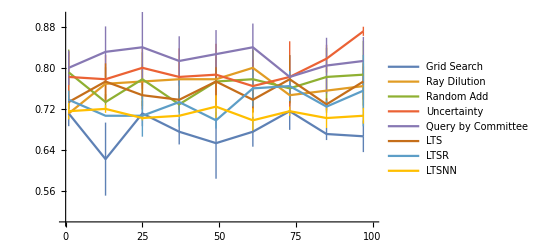

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]}][[Range[1,100,12]]]&/@{gs3DRes,rd3DRes,ra3DRes,u3DRes,qbc3DRes,lts3DRes,ltsr3DRes,ltsnn3DRes},PlotLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","Query by Committee","LTS","LTSR","LTSNN"},PlotRange->{{0,100},{0.5,0.9}}]
```

```mathematica
Table[TTest[Mean[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]][[Range[1,100,12]]]&/@{{gs3DRes,rd3DRes,ra3DRes,u3DRes,lts3DRes,ltsr3DRes,ltsnn3DRes}[[i]],qbc3DRes},Automatic,"TestDataTable"],{i,1,7}]
```

{ | Statistic | P-Value
T | -11.467 | 3.96232×10^-9, | Statistic | P-Value
T | -5.01624 | 0.000126653, | Statistic | P-Value
T | -4.91178 | 0.000156423, | Statistic | P-Value
T | -1.66672 | 0.115022, | Statistic | P-Value
T | -6.72753 | 4.85519×10^-6, | Statistic | P-Value
T | -8.07236 | 4.93307×10^-7, | Statistic | P-Value
T | -14.8877 | 8.56174×10^-9}

```mathematica
(* redo this for the 3 class problem *)
```

```mathematica
ensembleClf[clfs_,data_]:=Module[{decs,decCounts},
decs=Thread[Map[#[data]&,clfs]];
decCounts=Table[{Length[Select[decs[[j]],#=="ac"&]],Length[Select[decs[[j]],#=="bc"&]],Length[Select[decs[[j]],#=="none"&]]},{j,1,Length[decs]}] ;
(* {ac counts, bc counts, none counts} *)
Map[Which[
#[[1]]>#[[2]]&&#[[1]]>#[[3]],"ac",
#[[2]]>#[[1]]&&#[[2]]>#[[3]],"bc",
#[[3]]>#[[1]]&&#[[3]]>#[[2]],"none",
#[[1]]==#[[2]]&&#[[1]]==#[[3]],RandomChoice[{1/3,1/3,1/3}->{"ac","bc","none"}]
]&,decCounts]
]
```

```mathematica
N[Length[Select[MapThread[SameQ[#1,#2]&,{(ensembleClf[ltsnn3DClfs[[1]],test3D]),(ptClfy/@test3D)}],#==True&]]/Length[MapThread[SameQ[#1,#2]&,{(ensembleClf[ltsnn3DClfs[[1]],test3D]),(ptClfy/@test3D)}]]]
```

0.72

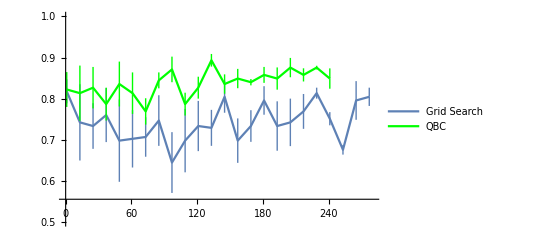

```mathematica
Show[ListLinePlot[Thread[{Range[Length@grid3DMore],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]}][[Range[1,Length@grid3DMore,12]]]&/@{gs3DMoreRes},PlotLegends->{"Grid Search"}],ListLinePlot[Thread[{Range[Length@pool3D],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]}][[Range[1,Length@pool3D,12]]]&/@{qbc3DMoreRes},PlotLegends->{"QBC"},PlotStyle->Green],PlotRange->{{0,280},{0.5,1}}]
```

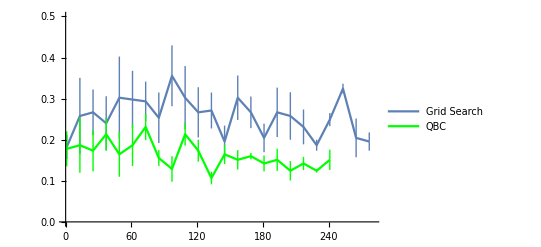

```mathematica
Show[ListLinePlot[Thread[{Range[Length@grid3DMore],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Error"]],{j,1,Length[#]}]]}][[Range[1,Length@grid3DMore,12]]]&/@{gs3DMoreRes},PlotLegends->{"Grid Search"}],ListLinePlot[Thread[{Range[Length@pool3D],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Error"]],{j,1,Length[#]}]]}][[Range[1,Length@pool3D,12]]]&/@{qbc3DMoreRes},PlotLegends->{"QBC"},PlotStyle->Green],PlotRange->{{0,280},{0,0.5}}]
```

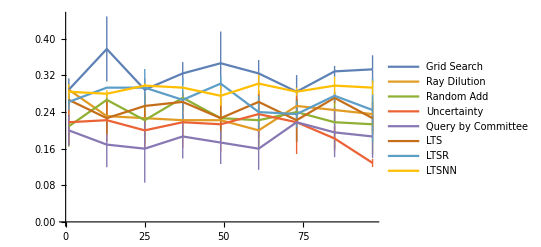

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Error"]],{j,1,Length[#]}]]}][[Range[1,100,12]]]&/@{gs3DRes,rd3DRes,ra3DRes,u3DRes,qbc3DRes,lts3DRes,ltsr3DRes,ltsnn3DRes},PlotLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","Query by Committee","LTS","LTSR","LTSNN"}]
```

### Noiseless, start at 5

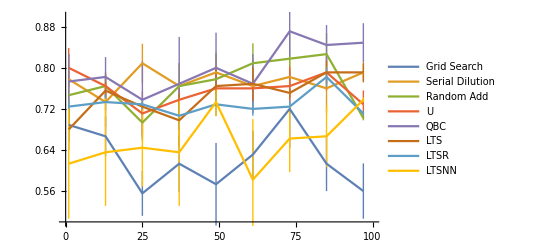

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]}][[Range[1,100,12]]]&/@{gs3D5Res,rd3D5Res,ra3D5Res,u3D5Res,qbc3D5Res,lts3D5Res,ltsr3D5Res,ltsnn3D5Res},PlotLegends->{"Grid Search","Serial Dilution","Random Add","U","QBC","LTS","LTSR","LTSNN"},PlotRange->{{0,100},{0.5,0.9}}]
```

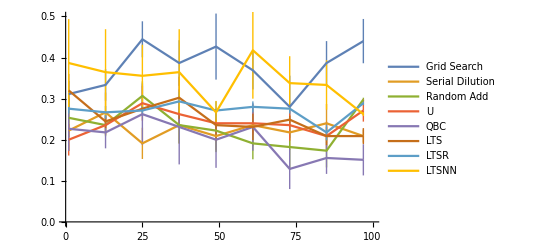

```mathematica
ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Error"]],{j,1,Length[#]}]]}][[Range[1,100,12]]]&/@{gs3D5Res,rd3D5Res,ra3D5Res,u3D5Res,qbc3D5Res,lts3D5Res,ltsr3D5Res,ltsnn3D5Res},PlotLegends->{"Grid Search","Serial Dilution","Random Add","U","QBC","LTS","LTSR","LTSNN"},PlotRange->{{0,100},{0,0.5}}]
```

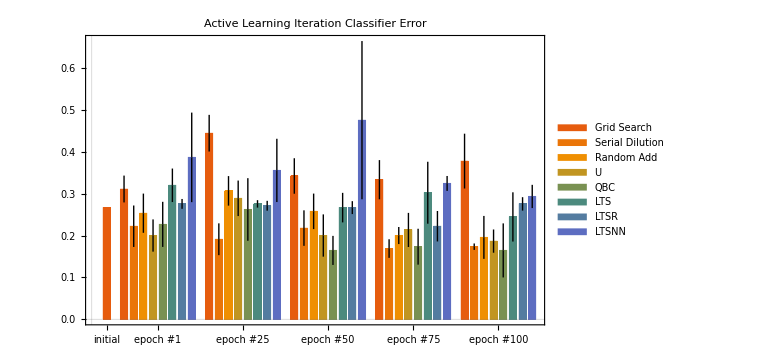

```mathematica
BarChart[Prepend[Thread[MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Error"]],{j,1,Length[#]}]][[Prepend[Range[25,100,25],1]]]&/@{gs3D5Res,rd3D5Res,ra3D5Res,u3D5Res,qbc3D5Res,lts3D5Res,ltsr3D5Res,ltsnn3D5Res}],{clfInit3D5Meas["Error"]}],PlotTheme->"Scientific",ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","U","QBC","LTS","LTSR","LTSNN"},{0.1,0.78}],PlotLabel->"Active Learning Iteration Classifier Error",ChartLabels->{{"initial","epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Large,LabelStyle->Black]
```

```mathematica
BarChart[Prepend[Thread[MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]][[Prepend[Range[25,100,25],1]]]&/@{gs3D5Res,rd3D5Res,ra3D5Res,u3D5Res,qbc3D5Res,lts3D5Res,ltsr3D5Res,ltsnn3D5Res}],{clfInit3D5Meas["Accuracy"]}],PlotTheme->"Scientific",ChartLegends->Placed[{"Grid Search","Serial Dilution","Random Add","U","QBC","LTS","LTSR","LTSNN"},{1,0.7}],PlotLabel->"Active Learning Iteration Classifier Error",ChartLabels->{{"initial","epoch #1","epoch #25","epoch #50","epoch #75","epoch #100"},None},ImageSize->Large,LabelStyle->Black]
```

-Graphics-

### Noise

#### Combined

```mathematica
pcRes3D={{gs3D10pcRes,rd3D10pcRes,ra3D10pcRes,u3D10pcRes,qbc3D10pcRes},{gs3D20pcRes,rd3D20pcRes,ra3D20pcRes,u3D20pcRes,qbc3D20pcRes},{gs3D30pcRes,rd3D30pcRes,ra3D30pcRes,u3D30pcRes,qbc3D30pcRes},{gs3D40pcRes,rd3D40pcRes,ra3D40pcRes,u3D40pcRes,qbc3D40pcRes},{gs3D50pcRes,rd3D50pcRes,ra3D50pcRes,u3D50pcRes,qbc3D50pcRes}};
```

```mathematica
Manipulate[ListLinePlot[Thread[{Range[100],MeanAround[#]&/@Thread[Table[Normal[#[[j]][All,"Accuracy"]],{j,1,Length[#]}]]}][[Range[1,100,12]]]&/@pcRes3D[[m]],PlotLegends->{"Grid Search","Ray Dilution","Random Add","Uncertainty","Query by Committee","LTS","LTSR","LTSNN"},PlotRange->{{0,100},{0.5,0.9}}],{m,{1,2,3,4,5}}];
```